# International Interaction Game

## Quantum-like Signorino’s Backward Induction Model

Quantum Extension of Signorino’s International Interaction Game Model

### Quantum-like Backward Induction Functions

```mathematica
(*Quantum Extension of Signorino's International Interaction Game Model Based on the classical implementation in signorino_model.m*)(*Quantum Backward Induction Functions*)q10quantum[theta1_,theta2_,U2War1_,U2Cap2_,l1_:1,l2_:1]:=Module[{numerator,denominator,exponentialFactor},numerator=Exp[l2*U2War1];
denominator=Exp[l2*U2War1]+Exp[l2*U2Cap2];
exponentialFactor=I*theta2;
Sqrt[numerator/denominator]*Exp[exponentialFactor]]

notq10quantum[theta1_,theta2_,U2War1_,U2Cap2_,l1_:1,l2_:1]:=Module[{numerator,denominator,exponentialFactor},numerator=Exp[l2*U2War1];
denominator=Exp[l2*U2War1]+Exp[l2*U2Cap2];
exponentialFactor=I*theta2;
Sqrt[1-numerator/denominator]*Exp[exponentialFactor]]

q11quantum[theta1_,theta2_,U2War1_,U2Cap2_,l1_:1,l2_:1]:=Module[{numerator,denominator,exponentialFactor},numerator=Exp[l2*U2War1];
denominator=Exp[l2*U2War1]+Exp[l2*U2Cap2];
exponentialFactor=I*theta2;
Sqrt[numerator/denominator]*Exp[exponentialFactor]]

notq11quantum[theta1_,theta2_,U2War1_,U2Cap2_,l1_:1,l2_:1]:=Module[{numerator,denominator,exponentialFactor},numerator=Exp[l2*U2War1];
denominator=Exp[l2*U2War1]+Exp[l2*U2Cap2];
exponentialFactor=I*theta2;
Sqrt[1-numerator/denominator]*Exp[exponentialFactor]]

p8quantum[theta1_,theta2_,U1War2_,U1Cap1_,l1_:1,l2_:1]:=Module[{numerator,denominator,exponentialFactor},numerator=Exp[l1*U1War2];
denominator=Exp[l1*U1War2]+Exp[l1*U1Cap1];
exponentialFactor=I*theta1;
Sqrt[numerator/denominator]*Exp[exponentialFactor]]

notp8quantum[theta1_,theta2_,U1War2_,U1Cap1_,l1_:1,l2_:1]:=Module[{numerator,denominator,exponentialFactor},numerator=Exp[l1*U1War2];
denominator=Exp[l1*U1War2]+Exp[l1*U1Cap1];
exponentialFactor=I*theta1;
Sqrt[1-numerator/denominator]*Exp[exponentialFactor]]

p12quantum[theta1_,theta2_,U1War2_,U1Cap1_,l1_:1,l2_:1]:=Module[{numerator,denominator,exponentialFactor},numerator=Exp[l1*U1War2];
denominator=Exp[l1*U1War2]+Exp[l1*U1Cap1];
exponentialFactor=I*theta1;
Sqrt[numerator/denominator]*Exp[exponentialFactor]]

notp12quantum[theta1_,theta2_,U1War2_,U1Cap1_,l1_:1,l2_:1]:=Module[{numerator,denominator,exponentialFactor},numerator=Exp[l1*U1War2];
denominator=Exp[l1*U1War2]+Exp[l1*U1Cap1];
exponentialFactor=I*theta1;
Sqrt[1-numerator/denominator]*Exp[exponentialFactor]]

q9quantum[theta1_,theta2_,U1War2_,U1Cap1_,U2War2_,U2Cap1_,U2Nego_,l1_:1,l2_:1]:=Module[{p12val,notp12val,UP2N12,numerator,denominator,exponentialFactor},p12val=p12quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
notp12val=notp12quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
UP2N12=p12val*U2War2+notp12val*U2Cap1;
numerator=Exp[l2*UP2N12];
denominator=Exp[l2*UP2N12]+Exp[l2*U2Nego];
exponentialFactor=I*theta2;
Sqrt[numerator/denominator]*Exp[exponentialFactor]]

notq9quantum[theta1_,theta2_,U1War2_,U1Cap1_,U2War2_,U2Cap1_,U2Nego_,l1_:1,l2_:1]:=Module[{p12val,notp12val,UP2N12,numerator,denominator,exponentialFactor},p12val=p12quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
notp12val=notp12quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
UP2N12=p12val*U2War2+notp12val*U2Cap1;
numerator=Exp[l2*UP2N12];
denominator=Exp[l2*UP2N12]+Exp[l2*U2Nego];
exponentialFactor=I*theta2;
Sqrt[1-numerator/denominator]*Exp[exponentialFactor]]

p7quantum[theta1_,theta2_,U1War1_,U1Cap2_,U2War1_,U2Cap2_,U1Nego_,l1_:1,l2_:1]:=Module[{q11val,notq11val,UP1N11,numerator,denominator,exponentialFactor},q11val=q11quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
notq11val=notq11quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
UP1N11=q11val*U1War1+notq11val*U1Cap2;
numerator=Exp[l1*UP1N11];
denominator=Exp[l1*UP1N11]+Exp[l1*U1Nego];
exponentialFactor=I*theta1;
Sqrt[numerator/denominator]*Exp[exponentialFactor]]

notp7quantum[theta1_,theta2_,U1War1_,U1Cap2_,U2War1_,U2Cap2_,U1Nego_,l1_:1,l2_:1]:=Module[{q11val,notq11val,UP1N11,numerator,denominator,exponentialFactor},q11val=q11quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
notq11val=notq11quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
UP1N11=q11val*U1War1+notq11val*U1Cap2;
numerator=Exp[l1*UP1N11];
denominator=Exp[l1*UP1N11]+Exp[l1*U1Nego];
exponentialFactor=I*theta1;
Sqrt[1-numerator/denominator]*Exp[exponentialFactor]]

q6quantum[theta1_,theta2_,U1War1_,U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_,l1_:1,l2_:1]:=Module[{p8val,notp8val,UP2N8,q11val,notq11val,U2N11,UP2N7,numerator,denominator,exponentialFactor},p8val=p8quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
notp8val=notp8quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
UP2N8=p8val*U2War2+notp8val*U2Cap1;
q11val=q11quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
notq11val=notq11quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
U2N11=q11val*U2War1+notq11val*U2Cap2;
UP2N7=p7quantum[theta1,theta2,U1War1,U1Cap2,U2War1,U2Cap2,U1Nego,l1,l2]*U2N11+notp7quantum[theta1,theta2,U1War1,U1Cap2,U2War1,U2Cap2,U1Nego,l1,l2]*U2Nego;
numerator=Exp[l2*UP2N8];
denominator=Exp[l2*UP2N8]+Exp[l2*UP2N7];
exponentialFactor=I*theta2;
Sqrt[numerator/denominator]*Exp[exponentialFactor]]

notq6quantum[theta1_,theta2_,U1War1_,U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_,l1_:1,l2_:1]:=Module[{p8val,notp8val,UP2N8,q11val,notq11val,U2N11,UP2N7,numerator,denominator,exponentialFactor},p8val=p8quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
notp8val=notp8quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
UP2N8=p8val*U2War2+notp8val*U2Cap1;
q11val=q11quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
notq11val=notq11quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
U2N11=q11val*U2War1+notq11val*U2Cap2;
UP2N7=p7quantum[theta1,theta2,U1War1,U1Cap2,U2War1,U2Cap2,U1Nego,l1,l2]*U2N11+notp7quantum[theta1,theta2,U1War1,U1Cap2,U2War1,U2Cap2,U1Nego,l1,l2]*U2Nego;
numerator=Exp[l2*UP2N8];
denominator=Exp[l2*UP2N8]+Exp[l2*UP2N7];
exponentialFactor=I*theta2;
Sqrt[1-numerator/denominator]*Exp[exponentialFactor]]

p5quantum[theta1_,theta2_,U1Cap1_,U2Cap1_,U1Cap2_,U2Cap2_,U1War1_,U2War1_,U1War2_,U2War2_,U1Nego_,U2Nego_,l1_:1,l2_:1]:=Module[{p12val,notp12val,UP1N12,q10val,notq10val,UP1N10,q9val,notq9val,UP1N9,numerator,denominator,exponentialFactor},p12val=p12quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
notp12val=notp12quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
UP1N12=p12val*U1War2+notp12val*U1Cap1;
q10val=q10quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
notq10val=notq10quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
UP1N10=q10val*U1War1+notq10val*U1Cap2;
q9val=q9quantum[theta1,theta2,U1War2,U1Cap1,U2War2,U2Cap1,U2Nego,l1,l2];
notq9val=notq9quantum[theta1,theta2,U1War2,U1Cap1,U2War2,U2Cap1,U2Nego,l1,l2];
UP1N9=q9val*UP1N12+notq9val*U1Nego;
numerator=Exp[l1*UP1N10];
denominator=Exp[l1*UP1N10]+Exp[l1*UP1N9];
exponentialFactor=I*theta1;
Sqrt[numerator/denominator]*Exp[exponentialFactor]]

notp5quantum[theta1_,theta2_,U1Cap1_,U2Cap1_,U1Cap2_,U2Cap2_,U1War1_,U2War1_,U1War2_,U2War2_,U1Nego_,U2Nego_,l1_:1,l2_:1]:=Module[{p12val,notp12val,UP1N12,q10val,notq10val,UP1N10,q9val,notq9val,UP1N9,numerator,denominator,exponentialFactor},p12val=p12quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
notp12val=notp12quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
UP1N12=p12val*U1War2+notp12val*U1Cap1;
q10val=q10quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
notq10val=notq10quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
UP1N10=q10val*U1War1+notq10val*U1Cap2;
q9val=q9quantum[theta1,theta2,U1War2,U1Cap1,U2War2,U2Cap1,U2Nego,l1,l2];
notq9val=notq9quantum[theta1,theta2,U1War2,U1Cap1,U2War2,U2Cap1,U2Nego,l1,l2];
UP1N9=q9val*UP1N12+notq9val*U1Nego;
numerator=Exp[l1*UP1N10];
denominator=Exp[l1*UP1N10]+Exp[l1*UP1N9];
exponentialFactor=I*theta1;
Sqrt[1-numerator/denominator]*Exp[exponentialFactor]]

p4quantum[theta1_,theta2_,U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_,U1Acq1_,l1_:1,l2_:1]:=Module[{q11val,notq11val,UP1N11,p8val,notp8val,UP1N8,p7val,notp7val,UP1N7,q6val,notq6val,UP1N6,numerator,denominator,exponentialFactor},q11val=q11quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
notq11val=notq11quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
UP1N11=q11val*U1War1+notq11val*U1Cap2;
p8val=p8quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
notp8val=notp8quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
UP1N8=p8val*U1War2+notp8val*U1Cap1;
p7val=p7quantum[theta1,theta2,U1War1,U1Cap2,U2War1,U2Cap2,U1Nego,l1,l2];
notp7val=notp7quantum[theta1,theta2,U1War1,U1Cap2,U2War1,U2Cap2,U1Nego,l1,l2];
UP1N7=p7val*UP1N11+notp7val*U1Nego;
q6val=q6quantum[theta1,theta2,U1War1,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego,l1,l2];
notq6val=notq6quantum[theta1,theta2,U1War1,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego,l1,l2];
UP1N6=q6val*UP1N8+notq6val*UP1N7;
numerator=Exp[l1*UP1N6];
denominator=Exp[l1*UP1N6]+Exp[l1*U1Acq1];
exponentialFactor=I*theta1;
Sqrt[numerator/denominator]*Exp[exponentialFactor]]

notp4quantum[theta1_,theta2_,U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_,U1Acq1_,l1_:1,l2_:1]:=Module[{q11val,notq11val,UP1N11,p8val,notp8val,UP1N8,p7val,notp7val,UP1N7,q6val,notq6val,UP1N6,numerator,denominator,exponentialFactor},q11val=q11quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
notq11val=notq11quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
UP1N11=q11val*U1War1+notq11val*U1Cap2;
p8val=p8quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
notp8val=notp8quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
UP1N8=p8val*U1War2+notp8val*U1Cap1;
p7val=p7quantum[theta1,theta2,U1War1,U1Cap2,U2War1,U2Cap2,U1Nego,l1,l2];
notp7val=notp7quantum[theta1,theta2,U1War1,U1Cap2,U2War1,U2Cap2,U1Nego,l1,l2];
UP1N7=p7val*UP1N11+notp7val*U1Nego;
q6val=q6quantum[theta1,theta2,U1War1,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego,l1,l2];
notq6val=notq6quantum[theta1,theta2,U1War1,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego,l1,l2];
UP1N6=q6val*UP1N8+notq6val*UP1N7;
numerator=Exp[l1*UP1N6];
denominator=Exp[l1*UP1N6]+Exp[l1*U1Acq1];
exponentialFactor=I*theta1;
Sqrt[1-numerator/denominator]*Exp[exponentialFactor]]

q3quantum[theta1_,theta2_,U1Cap1_,U2Cap1_,U1Cap2_,U2Cap2_,U1War1_,U2War1_,U1War2_,U2War2_,U1Nego_,U2Nego_,U2Acq2_,l1_:1,l2_:1]:=Module[{p12val,notp12val,UP2N12,q10val,notq10val,UP2N10,q9val,notq9val,UP2N9,p5val,notp5val,UP2N5,numerator,denominator,exponentialFactor},p12val=p12quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
notp12val=notp12quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
UP2N12=p12val*U2War2+notp12val*U2Cap1;
q10val=q10quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
notq10val=notq10quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
UP2N10=q10val*U2War1+notq10val*U2Cap2;
q9val=q9quantum[theta1,theta2,U1War2,U1Cap1,U2War2,U2Cap1,U2Nego,l1,l2];
notq9val=notq9quantum[theta1,theta2,U1War2,U1Cap1,U2War2,U2Cap1,U2Nego,l1,l2];
UP2N9=q9val*UP2N12+notq9val*U2Nego;
p5val=p5quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,l1,l2];
notp5val=notp5quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,l1,l2];
UP2N5=p5val*UP2N10+notp5val*UP2N9;
numerator=Exp[l2*UP2N5];
denominator=Exp[l2*UP2N5]+Exp[l2*U2Acq2];
exponentialFactor=I*theta2;
Sqrt[numerator/denominator]*Exp[exponentialFactor]]

notq3quantum[theta1_,theta2_,U1Cap1_,U2Cap1_,U1Cap2_,U2Cap2_,U1War1_,U2War1_,U1War2_,U2War2_,U1Nego_,U2Nego_,U2Acq2_,l1_:1,l2_:1]:=Module[{p12val,notp12val,UP2N12,q10val,notq10val,UP2N10,q9val,notq9val,UP2N9,p5val,notp5val,UP2N5,numerator,denominator,exponentialFactor},p12val=p12quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
notp12val=notp12quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
UP2N12=p12val*U2War2+notp12val*U2Cap1;
q10val=q10quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
notq10val=notq10quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
UP2N10=q10val*U2War1+notq10val*U2Cap2;
q9val=q9quantum[theta1,theta2,U1War2,U1Cap1,U2War2,U2Cap1,U2Nego,l1,l2];
notq9val=notq9quantum[theta1,theta2,U1War2,U1Cap1,U2War2,U2Cap1,U2Nego,l1,l2];
UP2N9=q9val*UP2N12+notq9val*U2Nego;
p5val=p5quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,l1,l2];
notp5val=notp5quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,l1,l2];
UP2N5=p5val*UP2N10+notp5val*UP2N9;
numerator=Exp[l2*UP2N5];
denominator=Exp[l2*UP2N5]+Exp[l2*U2Acq2];
exponentialFactor=I*theta2;
Sqrt[1-numerator/denominator]*Exp[exponentialFactor]]

q2quantum[theta1_,theta2_,U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U2SQ_,l1_:1,l2_:1]:=Module[{q11val,notq11val,UP2N11,p7val,notp7val,UP2N7,p8val,notp8val,UP2N8,q6val,notq6val,UP2N6,p4val,notp4val,UP2N4,numerator,denominator,exponentialFactor},q11val=q11quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
notq11val=notq11quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
UP2N11=q11val*U2War1+notq11val*U2Cap2;
p7val=p7quantum[theta1,theta2,U1War1,U1Cap2,U2War1,U2Cap2,U1Nego,l1,l2];
notp7val=notp7quantum[theta1,theta2,U1War1,U1Cap2,U2War1,U2Cap2,U1Nego,l1,l2];
UP2N7=p7val*UP2N11+notp7val*U2Nego;
p8val=p8quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
notp8val=notp8quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
UP2N8=p8val*U2War2+notp8val*U2Cap1;
q6val=q6quantum[theta1,theta2,U1War1,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego,l1,l2];
notq6val=notq6quantum[theta1,theta2,U1War1,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego,l1,l2];
UP2N6=q6val*UP2N8+notq6val*UP2N7;
p4val=p4quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,l1,l2];
notp4val=notp4quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,l1,l2];
UP2N4=p4val*UP2N6+notp4val*U2Acq1;
numerator=Exp[l2*UP2N4];
denominator=Exp[l2*UP2N4]+Exp[l2*U2SQ];
exponentialFactor=I*theta2;
Sqrt[numerator/denominator]*Exp[exponentialFactor]]

notq2quantum[theta1_,theta2_,U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U2SQ_,l1_:1,l2_:1]:=Module[{q11val,notq11val,UP2N11,p7val,notp7val,UP2N7,p8val,notp8val,UP2N8,q6val,notq6val,UP2N6,p4val,notp4val,UP2N4,numerator,denominator,exponentialFactor},q11val=q11quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
notq11val=notq11quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
UP2N11=q11val*U2War1+notq11val*U2Cap2;
p7val=p7quantum[theta1,theta2,U1War1,U1Cap2,U2War1,U2Cap2,U1Nego,l1,l2];
notp7val=notp7quantum[theta1,theta2,U1War1,U1Cap2,U2War1,U2Cap2,U1Nego,l1,l2];
UP2N7=p7val*UP2N11+notp7val*U2Nego;
p8val=p8quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
notp8val=notp8quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
UP2N8=p8val*U2War2+notp8val*U2Cap1;
q6val=q6quantum[theta1,theta2,U1War1,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego,l1,l2];
notq6val=notq6quantum[theta1,theta2,U1War1,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego,l1,l2];
UP2N6=q6val*UP2N8+notq6val*UP2N7;
p4val=p4quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,l1,l2];
notp4val=notp4quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,l1,l2];
UP2N4=p4val*UP2N6+notp4val*U2Acq1;
numerator=Exp[l2*UP2N4];
denominator=Exp[l2*UP2N4]+Exp[l2*U2SQ];
exponentialFactor=I*theta2;
Sqrt[1-numerator/denominator]*Exp[exponentialFactor]]

p1quantum[theta1_,theta2_,U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U1Acq2_,U2Acq2_,U1SQ_,U2SQ_,l1_:1,l2_:1]:=Module[{p12val,notp12val,UP1N12,q11val,notq11val,UP1N11,q9val,notq9val,UP1N9,p7val,notp7val,UP1N7,p8val,notp8val,UP1N8,q10val,notq10val,UP1N10,q6val,notq6val,UP1N6,p5val,notp5val,UP1N5,p4val,notp4val,UP1N4,q3val,notq3val,UP1N3,q2val,notq2val,UP1N2,numerator,denominator,exponentialFactor},p12val=p12quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
notp12val=notp12quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
UP1N12=p12val*U1War1+notp12val*U1Cap1;
q11val=q11quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
notq11val=notq11quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
UP1N11=q11val*U1War1+notq11val*U1Cap2;
q9val=q9quantum[theta1,theta2,U1War2,U1Cap1,U2War2,U2Cap1,U2Nego,l1,l2];
notq9val=notq9quantum[theta1,theta2,U1War2,U1Cap1,U2War2,U2Cap1,U2Nego,l1,l2];
UP1N9=q9val*UP1N12+notq9val*U1Nego;
p7val=p7quantum[theta1,theta2,U1War1,U1Cap2,U2War1,U2Cap2,U1Nego,l1,l2];
notp7val=notp7quantum[theta1,theta2,U1War1,U1Cap2,U2War1,U2Cap2,U1Nego,l1,l2];
UP1N7=p7val*UP1N11+notp7val*U1Nego;
p8val=p8quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
notp8val=notp8quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
UP1N8=p8val*U1War2+notp8val*U1Cap1;
q10val=q10quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
notq10val=notq10quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
UP1N10=q10val*U1War1+notq10val*U1Cap2;
q6val=q6quantum[theta1,theta2,U1War1,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego,l1,l2];
notq6val=notq6quantum[theta1,theta2,U1War1,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego,l1,l2];
UP1N6=q6val*UP1N8+notq6val*UP1N7;
p5val=p5quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,l1,l2];
notp5val=notp5quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,l1,l2];
UP1N5=p5val*UP1N10+notp5val*UP1N9;
p4val=p4quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,l1,l2];
notp4val=notp4quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,l1,l2];
UP1N4=p4val*UP1N6+notp4val*U1Acq1;
q3val=q3quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,U2Acq2,l1,l2];
notq3val=notq3quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,U2Acq2,l1,l2];
UP1N3=q3val*UP1N5+notq3val*U1Acq2;
q2val=q2quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U2SQ,l1,l2];
notq2val=notq2quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U2SQ,l1,l2];
UP1N2=q2val*UP1N4+notq2val*U1SQ;
numerator=Exp[l1*UP1N3];
denominator=Exp[l1*UP1N3]+Exp[l1*UP1N2];
exponentialFactor=I*theta1;
Sqrt[numerator/denominator]*Exp[exponentialFactor]]

notp1quantum[theta1_,theta2_,U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U1Acq2_,U2Acq2_,U1SQ_,U2SQ_,l1_:1,l2_:1]:=Module[{p12val,notp12val,UP1N12,q11val,notq11val,UP1N11,q9val,notq9val,UP1N9,p7val,notp7val,UP1N7,p8val,notp8val,UP1N8,q10val,notq10val,UP1N10,q6val,notq6val,UP1N6,p5val,notp5val,UP1N5,p4val,notp4val,UP1N4,q3val,notq3val,UP1N3,q2val,notq2val,UP1N2,numerator,denominator,exponentialFactor},p12val=p12quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
notp12val=notp12quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
UP1N12=p12val*U1War1+notp12val*U1Cap1;
q11val=q11quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
notq11val=notq11quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
UP1N11=q11val*U1War1+notq11val*U1Cap2;
q9val=q9quantum[theta1,theta2,U1War2,U1Cap1,U2War2,U2Cap1,U2Nego,l1,l2];
notq9val=notq9quantum[theta1,theta2,U1War2,U1Cap1,U2War2,U2Cap1,U2Nego,l1,l2];
UP1N9=q9val*UP1N12+notq9val*U1Nego;
p7val=p7quantum[theta1,theta2,U1War1,U1Cap2,U2War1,U2Cap2,U1Nego,l1,l2];
notp7val=notp7quantum[theta1,theta2,U1War1,U1Cap2,U2War1,U2Cap2,U1Nego,l1,l2];
UP1N7=p7val*UP1N11+notp7val*U1Nego;
p8val=p8quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
notp8val=notp8quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
UP1N8=p8val*U1War2+notp8val*U1Cap1;
q10val=q10quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
notq10val=notq10quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
UP1N10=q10val*U1War1+notq10val*U1Cap2;
q6val=q6quantum[theta1,theta2,U1War1,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego,l1,l2];
notq6val=notq6quantum[theta1,theta2,U1War1,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego,l1,l2];
UP1N6=q6val*UP1N8+notq6val*UP1N7;
p5val=p5quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,l1,l2];
notp5val=notp5quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,l1,l2];
UP1N5=p5val*UP1N10+notp5val*UP1N9;
p4val=p4quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,l1,l2];
notp4val=notp4quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,l1,l2];
UP1N4=p4val*UP1N6+notp4val*U1Acq1;
q3val=q3quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,U2Acq2,l1,l2];
notq3val=notq3quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,U2Acq2,l1,l2];
UP1N3=q3val*UP1N5+notq3val*U1Acq2;
q2val=q2quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U2SQ,l1,l2];
notq2val=notq2quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U2SQ,l1,l2];
UP1N2=q2val*UP1N4+notq2val*U1SQ;
numerator=Exp[l1*UP1N3];
denominator=Exp[l1*UP1N3]+Exp[l1*UP1N2];
exponentialFactor=I*theta1;
Sqrt[1-numerator/denominator]*Exp[exponentialFactor]]
```

### Outcome Functions

```mathematica
SQquantum[theta1_,theta2_,U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U1Acq2_,U2Acq2_,U1SQ_,U2SQ_,l1_:1,l2_:1]:=Module[{notp1,notq2},notp1=notp1quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,l1,l2];
notq2=notq2quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U2SQ,l1,l2];
notp1*notq2]

ACQ1quantum[theta1_,theta2_,U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U1Acq2_,U2Acq2_,U1SQ_,U2SQ_,l1_:1,l2_:1]:=Module[{notp1,q2,notp4},notp1=notp1quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,l1,l2];
q2=q2quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U2SQ,l1,l2];
notp4=notp4quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,l1,l2];
notp1*q2*notp4]

ACQ2quantum[theta1_,theta2_,U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U1Acq2_,U2Acq2_,U1SQ_,U2SQ_,l1_:1,l2_:1]:=Module[{p1,notq3},p1=p1quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,l1,l2];
notq3=notq3quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,U2Acq2,l1,l2];
p1*notq3]

NEGOquantum[theta1_,theta2_,U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U1Acq2_,U2Acq2_,U1SQ_,U2SQ_,l1_:1,l2_:1]:=Module[{p1,notp1,q2,q3,p4,notp5,notq6,notp7,notq9},p1=p1quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,l1,l2];
notp1=notp1quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,l1,l2];
q2=q2quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U2SQ,l1,l2];
q3=q3quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,U2Acq2,l1,l2];
p4=p4quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,l1,l2];
notp5=notp5quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,l1,l2];
notq6=notq6quantum[theta1,theta2,U1War1,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego,l1,l2];
notp7=notp7quantum[theta1,theta2,U1War1,U1Cap2,U2War1,U2Cap2,U1Nego,l1,l2];
notq9=notq9quantum[theta1,theta2,U1War2,U1Cap1,U2War2,U2Cap1,U2Nego,l1,l2];
notp1*q2*p4*notq6*notp7+p1*q3*notp5*notq9]

CAP1quantum[theta1_,theta2_,U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U1Acq2_,U2Acq2_,U1SQ_,U2SQ_,l1_:1,l2_:1]:=Module[{notp1,q2,p4,q6,notp8,p1,q3,notp5,q9,notp12},notp1=notp1quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,l1,l2];
q2=q2quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U2SQ,l1,l2];
p4=p4quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,l1,l2];
q6=q6quantum[theta1,theta2,U1War1,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego,l1,l2];
notp8=notp8quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
p1=p1quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,l1,l2];
q3=q3quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,U2Acq2,l1,l2];
notp5=notp5quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,l1,l2];
q9=q9quantum[theta1,theta2,U1War2,U1Cap1,U2War2,U2Cap1,U2Nego,l1,l2];
notp12=notp12quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
notp1*q2*p4*q6*notp8+p1*q3*notp5*q9*notp12]

CAP2quantum[theta1_,theta2_,U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U1Acq2_,U2Acq2_,U1SQ_,U2SQ_,l1_:1,l2_:1]:=Module[{notp1,q2,p4,notq6,p7,notq11,p1,q3,p5,notq10},notp1=notp1quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,l1,l2];
q2=q2quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U2SQ,l1,l2];
p4=p4quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,l1,l2];
notq6=notq6quantum[theta1,theta2,U1War1,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego,l1,l2];
p7=p7quantum[theta1,theta2,U1War1,U1Cap2,U2War1,U2Cap2,U1Nego,l1,l2];
notq11=notq11quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
p1=p1quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,l1,l2];
q3=q3quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,U2Acq2,l1,l2];
p5=p5quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,l1,l2];
notq10=notq10quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
notp1*q2*p4*notq6*p7*notq11+p1*q3*p5*notq10]

WAR1quantum[theta1_,theta2_,U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U1Acq2_,U2Acq2_,U1SQ_,U2SQ_,l1_:1,l2_:1]:=Module[{notp1,p1,q2,p4,notq6,p7,q11,q3,q10,p5},notp1=notp1quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,l1,l2];
p1=p1quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,l1,l2];
q2=q2quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U2SQ,l1,l2];
p4=p4quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,l1,l2];
notq6=notq6quantum[theta1,theta2,U1War1,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego,l1,l2];
p7=p7quantum[theta1,theta2,U1War1,U1Cap2,U2War1,U2Cap2,U1Nego,l1,l2];
q11=q11quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
q3=q3quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,U2Acq2,l1,l2];
q10=q10quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
p5=p5quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,l1,l2];
notp1*q2*p4*notq6*p7*q11+p1*q3*p5*q10]

WAR2quantum[theta1_,theta2_,U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U1Acq2_,U2Acq2_,U1SQ_,U2SQ_,l1_:1,l2_:1]:=Module[{notp1,p1,q2,p4,q6,p8,q3,notp5,q9,p12},notp1=notp1quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,l1,l2];
p1=p1quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,l1,l2];
q2=q2quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U2SQ,l1,l2];
p4=p4quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,l1,l2];
q6=q6quantum[theta1,theta2,U1War1,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego,l1,l2];
p8=p8quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
q3=q3quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,U2Acq2,l1,l2];
notp5=notp5quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,l1,l2];
q9=q9quantum[theta1,theta2,U1War2,U1Cap1,U2War2,U2Cap1,U2Nego,l1,l2];
p12=p12quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
notp1*q2*p4*q6*p8+p1*q3*notp5*q9*p12]
```

### Aux Functions

#### calculateQuantumOutcome

```mathematica
calculateQuantumOutcome[data_,rowIndex_Integer,theta1_:0,theta2_:0,l1_:1,l2_:1]:=Module[{utils,quantumAmplitudes,finalProbabilities,outcomes,outcomeProbs,maxVal,maxOutcomes,prediction,roundedProbs},

utils=extractUtilities[data,rowIndex];
If[utils===$Failed,
Return[$Failed]];

(*Compute quantum probability amplitudes*)
quantumAmplitudes=
Quiet[{
SQquantum[theta1,theta2,utils["U1War2"],utils["U1Cap1"],utils["U1Cap2"],
utils["U2War2"],utils["U2Cap1"],utils["U1War1"],utils["U2War1"],utils["U2Cap2"],
utils["U1Nego"],utils["U2Nego"],utils["U1Acq1"],utils["U2Acq1"],utils["U1Acq2"],
utils["U2Acq2"],utils["U1SQ"],utils["U2SQ"],l1,l2],

ACQ1quantum[theta1,theta2,utils["U1War2"],utils["U1Cap1"],utils["U1Cap2"],
utils["U2War2"],utils["U2Cap1"],utils["U1War1"],utils["U2War1"],utils["U2Cap2"],
utils["U1Nego"],utils["U2Nego"],utils["U1Acq1"],utils["U2Acq1"],utils["U1Acq2"],
utils["U2Acq2"],utils["U1SQ"],utils["U2SQ"],l1,l2],

ACQ2quantum[theta1,theta2,utils["U1War2"],utils["U1Cap1"],utils["U1Cap2"],utils["U2War2"],utils["U2Cap1"],utils["U1War1"],utils["U2War1"],utils["U2Cap2"],utils["U1Nego"],utils["U2Nego"],utils["U1Acq1"],utils["U2Acq1"],utils["U1Acq2"],utils["U2Acq2"],utils["U1SQ"],utils["U2SQ"],l1,l2],

NEGOquantum[theta1,theta2,utils["U1War2"],utils["U1Cap1"],utils["U1Cap2"],utils["U2War2"],utils["U2Cap1"],utils["U1War1"],utils["U2War1"],utils["U2Cap2"],utils["U1Nego"],utils["U2Nego"],utils["U1Acq1"],utils["U2Acq1"],utils["U1Acq2"],utils["U2Acq2"],utils["U1SQ"],utils["U2SQ"],l1,l2],

CAP1quantum[theta1,theta2,utils["U1War2"],utils["U1Cap1"],utils["U1Cap2"],utils["U2War2"],utils["U2Cap1"],utils["U1War1"],utils["U2War1"],utils["U2Cap2"],utils["U1Nego"],utils["U2Nego"],utils["U1Acq1"],utils["U2Acq1"],utils["U1Acq2"],utils["U2Acq2"],utils["U1SQ"],utils["U2SQ"],l1,l2],

CAP2quantum[theta1,theta2,utils["U1War2"],utils["U1Cap1"],utils["U1Cap2"],utils["U2War2"],utils["U2Cap1"],utils["U1War1"],utils["U2War1"],utils["U2Cap2"],utils["U1Nego"],utils["U2Nego"],utils["U1Acq1"],utils["U2Acq1"],utils["U1Acq2"],utils["U2Acq2"],utils["U1SQ"],utils["U2SQ"],l1,l2],

WAR1quantum[theta1,theta2,utils["U1War2"],utils["U1Cap1"],utils["U1Cap2"],utils["U2War2"],utils["U2Cap1"],utils["U1War1"],utils["U2War1"],utils["U2Cap2"],utils["U1Nego"],utils["U2Nego"],utils["U1Acq1"],utils["U2Acq1"],utils["U1Acq2"],utils["U2Acq2"],utils["U1SQ"],utils["U2SQ"],l1,l2],

WAR2quantum[theta1,theta2,utils["U1War2"],utils["U1Cap1"],utils["U1Cap2"],utils["U2War2"],utils["U2Cap1"],utils["U1War1"],utils["U2War1"],utils["U2Cap2"],utils["U1Nego"],utils["U2Nego"],utils["U1Acq1"],utils["U2Acq1"],utils["U1Acq2"],utils["U2Acq2"],utils["U1SQ"],utils["U2SQ"],l1,l2]
}];

(*Calculate final probabilities directly from amplitudes*)
finalProbabilities=Abs[#]^2&/@quantumAmplitudes;

(*Normalize probabilities*)
finalProbabilities=finalProbabilities/Total[finalProbabilities];

outcomes={"SQ","ACQ1","ACQ2","NEGO","CAP1","CAP2","WAR1","WAR2"};

(*Create outcome probabilities association for prediction*)
outcomeProbs=Association[MapThread[Rule,{outcomes,finalProbabilities}]];

(*Round probabilities to 4 decimal places for comparison*)
roundedProbs=Association[#->Round[outcomeProbs[#],0.0001]&/@Keys[outcomeProbs]];
maxVal=Max[Values[roundedProbs]];
maxOutcomes=Keys[Select[roundedProbs,#==maxVal&]];
(*Randomly select one if there are ties*)
prediction=RandomChoice[maxOutcomes];

Association[
"SQ"->finalProbabilities[[1]],
"ACQ1"->finalProbabilities[[2]],
"ACQ2"->finalProbabilities[[3]],
"NEGO"->finalProbabilities[[4]],
"CAP1"->finalProbabilities[[5]],
"CAP2"->finalProbabilities[[6]],
"WAR1"->finalProbabilities[[7]],
"WAR2"->finalProbabilities[[8]],
"prediction"->prediction,
"groundtruth"->utils["groundtruth"],
"utilities"->utils,
"theta1"->theta1,
"theta2"->theta2,
"l1"->l1,"l2"->l2,
"total"->Total[finalProbabilities]]]
```

#### getFirstNEntries

```mathematica
getFirstNEntries[resultAllData_,N_Integer]:=Module[{extractedEntries},
(*Input validation*)
If[!ListQ[resultAllData],
Print["Error: resultAllData must be a list"];
Return[$Failed]
];

If[N<=0,
Print["Error: N must be a positive integer"];
Return[$Failed]
];

If[Length[resultAllData]==0,
Print["Warning: resultAllData is empty"];
Return[{}]
];

(*Extract only the specified components from each entry*)
extractedEntries=
Table[Module[{entry,utils},
entry=resultAllData[[i]];
utils=If[KeyExistsQ[entry,"utilities"],entry["utilities"],Association[]];

Association[
"SQ"->If[KeyExistsQ[entry,"SQ"],Round[entry["SQ"],0.0001],0],
"ACQ1"->If[KeyExistsQ[entry,"ACQ1"],Round[entry["ACQ1"],0.0001],0],
"ACQ2"->If[KeyExistsQ[entry,"ACQ2"],Round[entry["ACQ2"],0.0001],0],
"NEGO"->If[KeyExistsQ[entry,"NEGO"],Round[entry["NEGO"],0.0001],0],
"CAP1"->If[KeyExistsQ[entry,"CAP1"],Round[entry["CAP1"],0.0001],0],
"CAP2"->If[KeyExistsQ[entry,"CAP2"],Round[entry["CAP2"],0.0001],0],
"WAR1"->If[KeyExistsQ[entry,"WAR1"],Round[entry["WAR1"],0.0001],0],
"WAR2"->If[KeyExistsQ[entry,"WAR2"],Round[entry["WAR2"],0.0001],0],
"prediction"->If[KeyExistsQ[entry,"prediction"],entry["prediction"],"UNKNOWN"],
"groundtruth"->If[KeyExistsQ[entry,"groundtruth"],entry["groundtruth"],"UNKNOWN"],
"Agent1"->If[KeyExistsQ[utils,"Agent1"],utils["Agent1"],"UNKNOWN"],
"Agent2"->If[KeyExistsQ[utils,"Agent2"],utils["Agent2"],"UNKNOWN"]]
],{i,Min[N,Length[resultAllData]]}
];

(*Return extracted entries with informative message*)
If[N>=Length[resultAllData],
Print["Note: Requested ",N," entries but only ",Length[resultAllData]," available. Returning all entries with extracted components."];
Return[extractedEntries],
Print["Returning first ",N," entries out of ",Length[resultAllData]," total entries with extracted components."];
Return[extractedEntries]]]
```

#### processQuantumDataset

```mathematica
(*Process Quantum Dataset*)
processQuantumDataset[data_,theta1_:0,theta2_:0,l1_:1,l2_:1]:=Module[{results,i},If[data===$Failed,Print["Error: Invalid data passed to processQuantumDataset"];
Return[{}]];
Print["Processing ",data["nrows"]," rows with quantum model..."];
Print["Parameters: θ1=",theta1,", θ2=",theta2,", λ1=",l1,", λ2=",l2];
results={};
Do[Module[{result},If[Mod[i,50]==0,Print["Processing row ",i,"/",data["nrows"]]];
result=calculateQuantumOutcome[data,i,theta1,theta2,l1,l2];
If[result=!=$Failed,AppendTo[results,result],Print["Warning: Failed to process row ",i]]],{i,1,data["nrows"]}];
Print["Successfully processed ",Length[results]," out of ",data["nrows"]," rows"];
results]
```

#### calculateQuantumAccuracy

```mathematica
calculateQuantumAccuracy[results_]:=Module[{predTruth,correct},If[Length[results]==0,Print["Warning: No results to calculate accuracy from"];
Return[0]];
predTruth=extractPredictionsAndGroundtruth[results];
If[Length[predTruth["predictions"]]==0,Print["Warning: No valid predictions found"];
Return[0]];
correct=MapThread[Equal,{predTruth["predictions"],predTruth["groundtruth"]}];
N[Count[correct,True]/Length[correct]]]
```

#### plotQuantumConfusionMatrix

```mathematica
plotQuantumConfusionMatrix[results_,theta1_:0,theta2_:0,l1_:1,l2_:1,title_:"Quantum Confusion Matrix"]:=Module[{predictions,groundTruths,outcomes,confusionData,accuracy,predTruth},If[Length[results]==0,Print["Warning: No results provided for confusion matrix"];
Return[Null]];
predTruth=extractPredictionsAndGroundtruth[results];
predictions=predTruth["predictions"];
groundTruths=predTruth["groundtruth"];
If[Length[predictions]==0,Print["Warning: No valid predictions found"];
Return[Null]];
accuracy=N[Count[MapThread[Equal,{predictions,groundTruths}],True]/Length[results]];
outcomes={"ACQ1","ACQ2","CAP1","CAP2","NEGO","SQ","WAR1"};
confusionData=Table[Count[MapThread[List,{groundTruths,predictions}],{actualOutcome,predictedOutcome}],{actualOutcome,outcomes},{predictedOutcome,outcomes}];
Print[Style[title,16,Bold]];
Print[Style["θ1 = "<>ToString[theta1]<>" θ2 = "<>ToString[theta2]<>" λ1 = "<>ToString[l1]<>" λ2 = "<>ToString[l2]<>" | Accuracy = "<>ToString[N[accuracy]],14]];
Print[""];
Grid[Prepend[MapThread[Prepend,{confusionData,outcomes}],Prepend[outcomes,Style["Actual \\ Predicted",Bold]]],Frame->All,Alignment->Center,Background->{None,{LightBlue,None}},ItemStyle->{Automatic,{Bold,Automatic}},Spacings->{2,1},FrameStyle->Thick,Dividers->{{2->Thick},{2->Thick}}]]
```

#### loadData

```mathematica
loadData[filename_String]:=Module[{rawData,headers,dataRows,groundtruth,utilityData,cleanedData,requiredColumns,missingColumns},

Print["Loading CSV file: ",filename];
rawData=Import[filename,"CSV"];

If[Head[rawData]=!=List||Length[rawData]<2,
Print["Error: Could not load CSV file or file is empty"];
Return[$Failed]
];

headers=First[rawData];
dataRows=Rest[rawData];

Print["Loaded ",Length[dataRows]," rows with ",Length[headers]," columns"];
cleanedData=Map[Function[row,Map[Function[cell,If[NumericQ[cell],cell,If[StringQ[cell]&&StringMatchQ[cell,NumberString],ToExpression[cell],cell]]],row]],dataRows];
groundtruth=cleanedData[[All,-1]];

utilityData=Association[Table[headers[[i]]->cleanedData[[All,i]],{i,Length[headers]}]];

requiredColumns={"wrTu1wr2","wrTu1cp1","wrTu1cp2","wrTu1wr1","wrTu1neg","wrTu1ac1","wrTu1ac2","wrTu1sq","wrTu2wr2","wrTu2cp1","wrTu2wr1","wrTu2cp2","wrTu2neg","wrTu2ac1","wrTu2ac2","wrTu2sq"};
missingColumns=Select[requiredColumns,!KeyExistsQ[utilityData,#]&];

If[Length[missingColumns]>0,
Print["Warning: Missing required columns: ",missingColumns];
];

Association[
"groundtruth"->groundtruth,
"data"->utilityData,
"nrows"->Length[cleanedData],
"headers"->headers,
"filename"->filename]
]
```

#### extractUtilities

```mathematica
extractUtilities[data_,rowIndex_Integer]:=Module[{row,utils},
If[rowIndex<1||rowIndex>data["nrows"],
Print["Error: Row index ",rowIndex," out of range [1, ",data["nrows"],"]"];
Return[$Failed]
];

row=data["data"];
utils=Association[];

(*Player 1 utilities*)
utils["U1War2"]=If[KeyExistsQ[row,"wrTu1wr2"]&&NumericQ[row["wrTu1wr2"][[rowIndex]]],row["wrTu1wr2"][[rowIndex]],0.0];
utils["U1Cap1"]=If[KeyExistsQ[row,"wrTu1cp1"]&&NumericQ[row["wrTu1cp1"][[rowIndex]]],row["wrTu1cp1"][[rowIndex]],0.0];
utils["U1Cap2"]=If[KeyExistsQ[row,"wrTu1cp2"]&&NumericQ[row["wrTu1cp2"][[rowIndex]]],row["wrTu1cp2"][[rowIndex]],0.0];
utils["U1War1"]=If[KeyExistsQ[row,"wrTu1wr1"]&&NumericQ[row["wrTu1wr1"][[rowIndex]]],row["wrTu1wr1"][[rowIndex]],0.0];
utils["U1Nego"]=If[KeyExistsQ[row,"wrTu1neg"]&&NumericQ[row["wrTu1neg"][[rowIndex]]],row["wrTu1neg"][[rowIndex]],0.0];
utils["U1Acq1"]=If[KeyExistsQ[row,"wrTu1ac1"]&&NumericQ[row["wrTu1ac1"][[rowIndex]]],row["wrTu1ac1"][[rowIndex]],0.0];
utils["U1Acq2"]=If[KeyExistsQ[row,"wrTu1ac2"]&&NumericQ[row["wrTu1ac2"][[rowIndex]]],row["wrTu1ac2"][[rowIndex]],0.0];
utils["U1SQ"]=If[KeyExistsQ[row,"wrTu1sq"]&&NumericQ[row["wrTu1sq"][[rowIndex]]],row["wrTu1sq"][[rowIndex]],0.0];

(*Player 2 utilities*)
utils["U2War2"]=If[KeyExistsQ[row,"wrTu2wr2"]&&NumericQ[row["wrTu2wr2"][[rowIndex]]],row["wrTu2wr2"][[rowIndex]],0.0];
utils["U2Cap1"]=If[KeyExistsQ[row,"wrTu2cp1"]&&NumericQ[row["wrTu2cp1"][[rowIndex]]],row["wrTu2cp1"][[rowIndex]],0.0];
utils["U2War1"]=If[KeyExistsQ[row,"wrTu2wr1"]&&NumericQ[row["wrTu2wr1"][[rowIndex]]],row["wrTu2wr1"][[rowIndex]],0.0];
utils["U2Cap2"]=If[KeyExistsQ[row,"wrTu2cp2"]&&NumericQ[row["wrTu2cp2"][[rowIndex]]],row["wrTu2cp2"][[rowIndex]],0.0];
utils["U2Nego"]=If[KeyExistsQ[row,"wrTu2neg"]&&NumericQ[row["wrTu2neg"][[rowIndex]]],row["wrTu2neg"][[rowIndex]],0.0];
utils["U2Acq1"]=If[KeyExistsQ[row,"wrTu2ac1"]&&NumericQ[row["wrTu2ac1"][[rowIndex]]],row["wrTu2ac1"][[rowIndex]],0.0];
utils["U2Acq2"]=If[KeyExistsQ[row,"wrTu2ac2"]&&NumericQ[row["wrTu2ac2"][[rowIndex]]],row["wrTu2ac2"][[rowIndex]],0.0];
utils["U2SQ"]=If[KeyExistsQ[row,"wrTu2sq"]&&NumericQ[row["wrTu2sq"][[rowIndex]]],row["wrTu2sq"][[rowIndex]],0.0];
utils["Agent1"]=If[KeyExistsQ[row,"ISOShNm1"],row["ISOShNm1"][[rowIndex]],"Unknown"];
utils["Agent2"]=If[KeyExistsQ[row,"ISOShNm2"],row["ISOShNm2"][[rowIndex]],"Unknown"];

(*Additional information*)
utils["groundtruth"]=data["groundtruth"][[rowIndex]];
utils["ccode1"]=If[KeyExistsQ[row,"ccode1"]&&NumericQ[row["ccode1"][[rowIndex]]],row["ccode1"][[rowIndex]],0];
utils["ccode2"]=If[KeyExistsQ[row,"ccode2"]&&NumericQ[row["ccode2"][[rowIndex]]],row["ccode2"][[rowIndex]],0];
utils["year"]=If[KeyExistsQ[row,"year"]&&NumericQ[row["year"][[rowIndex]]],row["year"][[rowIndex]],0];
utils]
```

#### extractPredictionsAndGroundtruth

```mathematica
extractPredictionsAndGroundtruth[results_]:=Module[{predictions,groundTruth,outcomes},
outcomes={"ACQ1","ACQ2","CAP1","CAP2","NEGO","SQ","WAR1"};
predictions=
Table[
Module[{outcomeProbs,maxVal,maxOutcome},
outcomeProbs=
Association[
"ACQ1"->If[KeyExistsQ[results[[i]],"ACQ1"]&&NumericQ[results[[i]]["ACQ1"]],results[[i]]["ACQ1"],0],
"ACQ2"->If[KeyExistsQ[results[[i]],"ACQ2"]&&NumericQ[results[[i]]["ACQ2"]],results[[i]]["ACQ2"],0],
"CAP1"->If[KeyExistsQ[results[[i]],"CAP1"]&&NumericQ[results[[i]]["CAP1"]],results[[i]]["CAP1"],0],
"CAP2"->If[KeyExistsQ[results[[i]],"CAP2"]&&NumericQ[results[[i]]["CAP2"]],results[[i]]["CAP2"],0],
"NEGO"->If[KeyExistsQ[results[[i]],"NEGO"]&&NumericQ[results[[i]]["NEGO"]],results[[i]]["NEGO"],0],
"SQ"->If[KeyExistsQ[results[[i]],"SQ"]&&NumericQ[results[[i]]["SQ"]],results[[i]]["SQ"],0],
"WAR1"->If[KeyExistsQ[results[[i]],"WAR1"]&&NumericQ[results[[i]]["WAR1"]],results[[i]]["WAR1"],0]
];

(*Find outcome with maximum probability*)
maxVal=Max[Values[outcomeProbs]];
maxOutcome=First[Keys[Select[outcomeProbs,#==maxVal&]]];
maxOutcome],{i,Length[results]}];

groundTruth=Table[If[KeyExistsQ[results[[i]],"groundtruth"],results[[i]]["groundtruth"],"UNKNOWN"],{i,Length[results]}];
Association[
"predictions"->predictions,
"groundtruth"->groundTruth]]
```

### Optimization Functions

```mathematica
(*Grid Search Function for Optimal Theta Parameters*)
gridSearchQuantumThetas[data_,theta1Range_List,theta2Range_List,l1_:1,l2_:1,verbose_:True]:=Module[{results,bestAccuracy,bestTheta1,bestTheta2,totalCombinations,currentCombination,startTime,gridResults,theta1Values,theta2Values},(*Input validation*)If[data===$Failed||!KeyExistsQ[data,"nrows"],Print["Error: Invalid data provided"];
Return[$Failed]];
(*Extract theta values from ranges*)theta1Values=theta1Range;
theta2Values=theta2Range;
totalCombinations=Length[theta1Values]*Length[theta2Values];
currentCombination=0;
bestAccuracy=0;
bestTheta1=First[theta1Values];
bestTheta2=First[theta2Values];
If[verbose,Print["Starting grid search over ",totalCombinations," parameter combinations..."];
Print["Theta1 range: ",theta1Values];
Print["Theta2 range: ",theta2Values];
Print["Lambda1 = ",l1,", Lambda2 = ",l2];
Print["Dataset size: ",data["nrows"]," rows"];
Print[""];];
startTime=AbsoluteTime[];
gridResults={};
(*Grid search loop*)Do[Module[{currentResults,currentAccuracy,elapsedTime,estimatedTotal,estimatedRemaining},currentCombination++;
If[verbose&&Mod[currentCombination,Max[1,Floor[totalCombinations/20]]]==0,elapsedTime=AbsoluteTime[]-startTime;
estimatedTotal=elapsedTime*totalCombinations/currentCombination;
estimatedRemaining=estimatedTotal-elapsedTime;
Print["Progress: ",currentCombination,"/",totalCombinations," (",N[100*currentCombination/totalCombinations,3],"%)"];
Print["Elapsed: ",N[elapsedTime/60,2]," min, Estimated remaining: ",N[estimatedRemaining/60,2]," min"];
Print["Current best: θ1=",bestTheta1,", θ2=",bestTheta2,", Accuracy=",N[bestAccuracy,4]];
Print[""];];
(*Calculate results for current theta combination*)currentResults=Quiet[processQuantumDataset[data,theta1,theta2,l1,l2]];
If[Length[currentResults]>0,currentAccuracy=calculateQuantumAccuracy[currentResults];
(*Store result*)AppendTo[gridResults,Association["theta1"->theta1,"theta2"->theta2,"accuracy"->currentAccuracy,"l1"->l1,"l2"->l2]];
(*Update best parameters if current is better*)If[currentAccuracy>bestAccuracy,bestAccuracy=currentAccuracy;
bestTheta1=theta1;
bestTheta2=theta2;
If[verbose,Print["New best found: θ1=",theta1,", θ2=",theta2,", Accuracy=",N[currentAccuracy,4]];];];,(*Handle failed calculation*)If[verbose,Print["Warning: Failed to calculate results for θ1=",theta1,", θ2=",theta2];];
AppendTo[gridResults,Association["theta1"->theta1,"theta2"->theta2,"accuracy"->0,"l1"->l1,"l2"->l2,"failed"->True]];];],{theta1,theta1Values},{theta2,theta2Values}];
If[verbose,Print["Grid search completed!"];
Print["Total time: ",N[(AbsoluteTime[]-startTime)/60,2]," minutes"];
Print["Best parameters found:"];
Print["  θ1 = ",bestTheta1];
Print["  θ2 = ",bestTheta2];
Print["  Accuracy = ",N[bestAccuracy,4]];
Print[""];];
(*Return comprehensive results*)Association["bestTheta1"->bestTheta1,"bestTheta2"->bestTheta2,"bestAccuracy"->bestAccuracy,"allResults"->gridResults,"totalCombinations"->totalCombinations,"l1"->l1,"l2"->l2]]

(*Helper function to create parameter ranges*)
createThetaRange[min_,max_,steps_]:=If[steps==1,{min},Range[min,max,(max-min)/(steps-1)]]

(*Function to visualize grid search results*)
visualizeGridSearchResults[gridSearchResults_]:=Module[{validResults,heatmapData,theta1Values,theta2Values,accuracyMatrix,minAcc,maxAcc,tickLabels1,tickLabels2,theta1Ticks,theta2Ticks,bestIndex,plot},(*Check if this is a proper grid search result structure*)If[!AssociationQ[gridSearchResults]||!KeyExistsQ[gridSearchResults,"allResults"],Print["Error: Input must be a grid search results Association with 'allResults' key"];
Print["Use gridSearchQuantumThetas[] to generate proper grid search results"];
Return[Null];];
validResults=Select[gridSearchResults["allResults"],!KeyExistsQ[#,"failed"]&];
If[Length[validResults]==0,Print["No valid results to visualize"];
Return[Null];];
theta1Values=Sort[DeleteDuplicates[#["theta1"]&/@validResults]];
theta2Values=Sort[DeleteDuplicates[#["theta2"]&/@validResults]];
(*Create accuracy matrix for heatmap*)accuracyMatrix=Table[Module[{matchingResult},matchingResult=SelectFirst[validResults,#["theta1"]==theta1&&#["theta2"]==theta2&];
If[matchingResult===Missing["NotFound"],0,matchingResult["accuracy"]]],{theta1,theta1Values},{theta2,theta2Values}];
(*Calculate min/max for better color scaling*)minAcc=Min[Flatten[accuracyMatrix]];
maxAcc=Max[Flatten[accuracyMatrix]];
(*Create proper tick labels*)tickLabels1=Table[{i,NumberForm[N[theta1Values[[i]],3],{4,3}]},{i,Length[theta1Values]}];
tickLabels2=Table[{i,NumberForm[N[theta2Values[[i]],3],{4,3}]},{i,Length[theta2Values]}];
(*Find position of best result for highlighting*)bestIndex=Position[accuracyMatrix,maxAcc];
Print[Style["Grid Search Results Visualization",16,Bold]];
Print[Style[StringJoin["Parameter Space: ",ToString[Length[theta1Values]]," × ",ToString[Length[theta2Values]]," = ",ToString[Length[validResults]]," combinations"],14]];
Print[Style[StringJoin["Best Parameters: θ₁ = ",ToString[NumberForm[N[gridSearchResults["bestTheta1"],4],{5,4}]],", θ₂ = ",ToString[NumberForm[N[gridSearchResults["bestTheta2"],4],{5,4}]]," → Accuracy = ",ToString[NumberForm[N[gridSearchResults["bestAccuracy"],4],{5,4}]]," (",ToString[NumberForm[100*N[gridSearchResults["bestAccuracy"]],{5,2}]],"%)"],14,RGBColor[0.1,0.5,0.1]]];
Print[Style[StringJoin["Accuracy Range: ",ToString[NumberForm[N[minAcc],{4,3}]]," - ",ToString[NumberForm[N[maxAcc],{4,3}]]],12,Gray]];
Print[""];
(*Create improved heatmap*)plot=ArrayPlot[Transpose[accuracyMatrix],(*Professional color scheme*)ColorFunction->(Blend[{RGBColor[0.2,0.2,0.4],(*Dark blue for low values*)RGBColor[0.3,0.6,0.8],(*Medium blue*)RGBColor[0.9,0.9,0.3],(*Yellow for medium values*)RGBColor[0.9,0.6,0.1],(*Orange*)RGBColor[0.8,0.2,0.2]     (*Red for high values*)},#]&),ColorFunctionScaling->True,(*Proper labels and ticks*)PlotLabel->Style["Parameter Optimization Heatmap",16,Bold],FrameLabel->{Style["θ₁ (Player 1 Quantum Phase)",14,Bold],Style["θ₂ (Player 2 Quantum Phase)",14,Bold]},(*Custom ticks with actual parameter values*)FrameTicks->{{tickLabels2,None},(*Bottom ticks for theta2*){tickLabels1,None}   (*Left ticks for theta1*)},(*Plot options*)AspectRatio->Automatic,ImageSize->{500,400},Frame->True,FrameStyle->Black,PlotRangePadding->None,(*Color bar legend*)PlotLegends->Placed[BarLegend[{Blend[{RGBColor[0.2,0.2,0.4],RGBColor[0.3,0.6,0.8],RGBColor[0.9,0.9,0.3],RGBColor[0.9,0.6,0.1],RGBColor[0.8,0.2,0.2]},#]&,{minAcc,maxAcc}},LegendLabel->Style["Accuracy",12,Bold],LegendMarkerSize->200],Right]];
(*Add text annotations for best points if there are few enough points*)If[Length[validResults]<=25,plot=Show[plot,Graphics[{White,EdgeForm[{Thick,Black}],Table[Module[{acc,pos1,pos2},acc=accuracyMatrix[[i,j]];
pos1=j;pos2=i;
If[acc==maxAcc,{Red,EdgeForm[{Thick,Red}],Rectangle[{pos1-0.4,pos2-0.4},{pos1+0.4,pos2+0.4}]},If[acc>0.8*maxAcc,Text[Style[NumberForm[acc,{3,3}],10,Bold,White],{pos1,pos2}],Text[Style[NumberForm[acc,{3,3}],9,Black],{pos1,pos2}]]]],{i,Length[theta1Values]},{j,Length[theta2Values]}]}]]];
(*Display summary statistics*)Print[Style["Summary Statistics:",14,Bold]];
Print["• Mean Accuracy: ",NumberForm[Mean[Flatten[accuracyMatrix]],{4,3}]];
Print["• Standard Deviation: ",NumberForm[StandardDeviation[Flatten[accuracyMatrix]],{4,3}]];
Print["• Improvement over Random: ",NumberForm[100*(maxAcc-1/7),{4,2}],"% points"];
plot]

(*Function to get top N parameter combinations*)
getTopParameterCombinations[gridSearchResults_,n_:5]:=Module[{validResults,sortedResults},validResults=Select[gridSearchResults["allResults"],!KeyExistsQ[#,"failed"]&];
sortedResults=Reverse[SortBy[validResults,#["accuracy"]&]];
Take[sortedResults,Min[n,Length[sortedResults]]]]

(*For a focused search around your current parameters:*)
focusedSearchAroundCurrent[data_,currentTheta1_,currentTheta2_,rangeSize_:1.0,gridSize_:5]:=Module[{theta1Range,theta2Range,results},Print["Running focused search around θ1=",currentTheta1,", θ2=",currentTheta2];
theta1Range=createThetaRange[currentTheta1-rangeSize,currentTheta1+rangeSize,gridSize];
theta2Range=createThetaRange[currentTheta2-rangeSize,currentTheta2+rangeSize,gridSize];
Print["θ1 range: ",theta1Range];
Print["θ2 range: ",theta2Range];
results=gridSearchQuantumThetas[data,theta1Range,theta2Range,1,1,True];
Print["Focused search completed. Visualizing results..."];
visualizeGridSearchResults[results];
results]

(*Simple function to analyze current results *)analyzeCurrentResults[quantumResults_List]:=Module[{accuracy,sampleResult,theta1Val,theta2Val,predTruth},If[Length[quantumResults]==0,Print["No results to analyze"];
Return[$Failed];];
(*Get sample result to extract theta values*)sampleResult=First[quantumResults];
theta1Val=sampleResult["theta1"];
theta2Val=sampleResult["theta2"];
(*Calculate accuracy*)accuracy=calculateQuantumAccuracy[quantumResults];
(*Get predictions and ground truth*)predTruth=extractPredictionsAndGroundtruth[quantumResults];
Print["=== Quantum Model Analysis ==="];
Print["Parameters: θ1 = ",N[theta1Val,4]," (",theta1Val,")"];
Print["           θ2 = ",N[theta2Val,4]," (",theta2Val,")"];
Print["Total cases: ",Length[quantumResults]];
Print["Accuracy: ",N[accuracy,4]," (",N[100*accuracy,2],"%)"];
Print[""];
(*Show outcome distribution*)Module[{outcomes,counts},outcomes={"SQ","ACQ1","ACQ2","NEGO","CAP1","CAP2","WAR1","WAR2"};
counts=Table[Count[predTruth["predictions"],outcome],{outcome,outcomes}];
Print["Prediction distribution:"];
Do[If[counts[[i]]>0,Print["  ",outcomes[[i]],": ",counts[[i]]," (",N[100*counts[[i]]/Length[predTruth["predictions"]],1],"%)"]],{i,Length[outcomes]}];];
Print[""];
(*Show confusion matrix*)plotQuantumConfusionMatrix[quantumResults,theta1Val,theta2Val,1,1,"Current Quantum Model Results"];
Association["accuracy"->accuracy,"theta1"->theta1Val,"theta2"->theta2Val,"totalCases"->Length[quantumResults],"predictions"->predTruth["predictions"],"groundTruth"->predTruth["groundtruth"]]]
```

## Experiments

### Balanced Dataset

#### Setting 1: Lamda1 = 1 | Lambda2 = 1

```mathematica
datasetPath = "/Users/162191/Documents/GitHub/quantum_international_interaction_game/dataset/balanced_data.csv"
(* "D:\\home\\Documents\\Github\\quantum_international_interaction_game\\dataset\\balanced_data.csv"; *)
data=loadData[datasetPath];
```

/Users/162191/Documents/GitHub/quantum_international_interaction_game/dataset/balanced_data.csv

Loading CSV file: /Users/162191/Documents/GitHub/quantum_international_interaction_game/dataset/balanced_data.csv

Loaded 579 rows with 149 columns

```mathematica
gridsize = 8;
l1 =1;
l2=1;
theta1Range=createThetaRange[0,2*Pi,gridsize];
theta2Range=createThetaRange[0,2*Pi,gridsize];
```

```mathematica
gridResults=gridSearchQuantumThetas[data,theta1Range,theta2Range,l1,l2];
Print["Best parameters: θ1=",gridResults["bestTheta1"],", θ2=",gridResults["bestTheta2"]];
Print["Best accuracy: ",gridResults["bestAccuracy"]];
```

Starting grid search over 64 parameter combinations...

Theta1 range: {0,(2 π)/7,(4 π)/7,(6 π)/7,(8 π)/7,(10 π)/7,(12 π)/7,2 π}

Theta2 range: {0,(2 π)/7,(4 π)/7,(6 π)/7,(8 π)/7,(10 π)/7,(12 π)/7,2 π}

Lambda1 = 1, Lambda2 = 1

Dataset size: 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=0, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

New best found: θ1=0, θ2=0, Accuracy=0.174439

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=(2 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

New best found: θ1=0, θ2=(2 π)/7, Accuracy=0.184801

Progress: 3/64 (4.69%)

Elapsed: 0.79 min, Estimated remaining: 16. min

Current best: θ1=0, θ2=(2 π)/7, Accuracy=0.184801

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=(4 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=(6 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=(8 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 6/64 (9.38%)

Elapsed: 2.1 min, Estimated remaining: 21. min

Current best: θ1=0, θ2=(2 π)/7, Accuracy=0.184801

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=(10 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=(12 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=2 π, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 9/64 (14.1%)

Elapsed: 3.5 min, Estimated remaining: 21. min

Current best: θ1=0, θ2=(2 π)/7, Accuracy=0.184801

Processing 579 rows with quantum model...

Parameters: θ1=(2 π)/7, θ2=0, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(2 π)/7, θ2=(2 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(2 π)/7, θ2=(4 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 12/64 (18.8%)

Elapsed: 4.9 min, Estimated remaining: 21. min

Current best: θ1=0, θ2=(2 π)/7, Accuracy=0.184801

Processing 579 rows with quantum model...

Parameters: θ1=(2 π)/7, θ2=(6 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(2 π)/7, θ2=(8 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(2 π)/7, θ2=(10 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 15/64 (23.4%)

Elapsed: 6.4 min, Estimated remaining: 21. min

Current best: θ1=0, θ2=(2 π)/7, Accuracy=0.184801

Processing 579 rows with quantum model...

Parameters: θ1=(2 π)/7, θ2=(12 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(2 π)/7, θ2=2 π, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(4 π)/7, θ2=0, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

New best found: θ1=(4 π)/7, θ2=0, Accuracy=0.205527

Progress: 18/64 (28.1%)

Elapsed: 7.7 min, Estimated remaining: 20. min

Current best: θ1=(4 π)/7, θ2=0, Accuracy=0.205527

Processing 579 rows with quantum model...

Parameters: θ1=(4 π)/7, θ2=(2 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(4 π)/7, θ2=(4 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(4 π)/7, θ2=(6 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 21/64 (32.8%)

Elapsed: 9.2 min, Estimated remaining: 19. min

Current best: θ1=(4 π)/7, θ2=0, Accuracy=0.205527

Processing 579 rows with quantum model...

Parameters: θ1=(4 π)/7, θ2=(8 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(4 π)/7, θ2=(10 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(4 π)/7, θ2=(12 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

New best found: θ1=(4 π)/7, θ2=(12 π)/7, Accuracy=0.207254

Progress: 24/64 (37.5%)

Elapsed: 11. min, Estimated remaining: 18. min

Current best: θ1=(4 π)/7, θ2=(12 π)/7, Accuracy=0.207254

Processing 579 rows with quantum model...

Parameters: θ1=(4 π)/7, θ2=2 π, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(6 π)/7, θ2=0, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(6 π)/7, θ2=(2 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 27/64 (42.2%)

Elapsed: 12. min, Estimated remaining: 17. min

Current best: θ1=(4 π)/7, θ2=(12 π)/7, Accuracy=0.207254

Processing 579 rows with quantum model...

Parameters: θ1=(6 π)/7, θ2=(4 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

New best found: θ1=(6 π)/7, θ2=(4 π)/7, Accuracy=0.214162

Processing 579 rows with quantum model...

Parameters: θ1=(6 π)/7, θ2=(6 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(6 π)/7, θ2=(8 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 30/64 (46.9%)

Elapsed: 14. min, Estimated remaining: 15. min

Current best: θ1=(6 π)/7, θ2=(4 π)/7, Accuracy=0.214162

Processing 579 rows with quantum model...

Parameters: θ1=(6 π)/7, θ2=(10 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(6 π)/7, θ2=(12 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(6 π)/7, θ2=2 π, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 33/64 (51.6%)

Elapsed: 15. min, Estimated remaining: 14. min

Current best: θ1=(6 π)/7, θ2=(4 π)/7, Accuracy=0.214162

Processing 579 rows with quantum model...

Parameters: θ1=(8 π)/7, θ2=0, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(8 π)/7, θ2=(2 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(8 π)/7, θ2=(4 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 36/64 (56.3%)

Elapsed: 16. min, Estimated remaining: 13. min

Current best: θ1=(6 π)/7, θ2=(4 π)/7, Accuracy=0.214162

Processing 579 rows with quantum model...

Parameters: θ1=(8 π)/7, θ2=(6 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(8 π)/7, θ2=(8 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(8 π)/7, θ2=(10 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 39/64 (60.9%)

Elapsed: 18. min, Estimated remaining: 12. min

Current best: θ1=(6 π)/7, θ2=(4 π)/7, Accuracy=0.214162

Processing 579 rows with quantum model...

Parameters: θ1=(8 π)/7, θ2=(12 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(8 π)/7, θ2=2 π, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(10 π)/7, θ2=0, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 42/64 (65.6%)

Elapsed: 19. min, Estimated remaining: 10. min

Current best: θ1=(6 π)/7, θ2=(4 π)/7, Accuracy=0.214162

Processing 579 rows with quantum model...

Parameters: θ1=(10 π)/7, θ2=(2 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(10 π)/7, θ2=(4 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(10 π)/7, θ2=(6 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 45/64 (70.3%)

Elapsed: 21. min, Estimated remaining: 8.8 min

Current best: θ1=(6 π)/7, θ2=(4 π)/7, Accuracy=0.214162

Processing 579 rows with quantum model...

Parameters: θ1=(10 π)/7, θ2=(8 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(10 π)/7, θ2=(10 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(10 π)/7, θ2=(12 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 48/64 (75.%)

Elapsed: 22. min, Estimated remaining: 7.5 min

Current best: θ1=(6 π)/7, θ2=(4 π)/7, Accuracy=0.214162

Processing 579 rows with quantum model...

Parameters: θ1=(10 π)/7, θ2=2 π, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(12 π)/7, θ2=0, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(12 π)/7, θ2=(2 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 51/64 (79.7%)

Elapsed: 24. min, Estimated remaining: 6.1 min

Current best: θ1=(6 π)/7, θ2=(4 π)/7, Accuracy=0.214162

Processing 579 rows with quantum model...

Parameters: θ1=(12 π)/7, θ2=(4 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(12 π)/7, θ2=(6 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(12 π)/7, θ2=(8 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 54/64 (84.4%)

Elapsed: 25. min, Estimated remaining: 4.7 min

Current best: θ1=(6 π)/7, θ2=(4 π)/7, Accuracy=0.214162

Processing 579 rows with quantum model...

Parameters: θ1=(12 π)/7, θ2=(10 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(12 π)/7, θ2=(12 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(12 π)/7, θ2=2 π, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 57/64 (89.1%)

Elapsed: 27. min, Estimated remaining: 3.3 min

Current best: θ1=(6 π)/7, θ2=(4 π)/7, Accuracy=0.214162

Processing 579 rows with quantum model...

Parameters: θ1=2 π, θ2=0, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=2 π, θ2=(2 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=2 π, θ2=(4 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 60/64 (93.8%)

Elapsed: 28. min, Estimated remaining: 1.9 min

Current best: θ1=(6 π)/7, θ2=(4 π)/7, Accuracy=0.214162

Processing 579 rows with quantum model...

Parameters: θ1=2 π, θ2=(6 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=2 π, θ2=(8 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=2 π, θ2=(10 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 63/64 (98.4%)

Elapsed: 30. min, Estimated remaining: 0.47 min

Current best: θ1=(6 π)/7, θ2=(4 π)/7, Accuracy=0.214162

Processing 579 rows with quantum model...

Parameters: θ1=2 π, θ2=(12 π)/7, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=2 π, θ2=2 π, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Grid search completed!

Total time: 31. minutes

Best parameters found:

θ1 = (6 π)/7

θ2 = (4 π)/7

Accuracy = 0.214162

Best parameters: θ1=(6 π)/7, θ2=(4 π)/7

Best accuracy: 0.214162

```mathematica
analyzeCurrentResults[gridResults]
```

analyzeCurrentResults[<|bestTheta1→(6 π)/7,bestTheta2→(4 π)/7,bestAccuracy→0.214162,allResults→{<|theta1→0,theta2→0,accuracy→0.174439,l1→1,l2→1|>,<|theta1→0,theta2→(2 π)/7,accuracy→0.184801,l1→1,l2→1|>,<|theta1→0,theta2→(4 π)/7,accuracy→0.160622,l1→1,l2→1|>,<|theta1→0,theta2→(6 π)/7,accuracy→0.170984,l1→1,l2→1|>,<|theta1→0,theta2→(8 π)/7,accuracy→0.170984,l1→1,l2→1|>,<|theta1→0,theta2→(10 π)/7,accuracy→0.160622,l1→1,l2→1|>,<|theta1→0,theta2→(12 π)/7,accuracy→0.184801,l1→1,l2→1|>,<|theta1→0,theta2→2 π,accuracy→0.174439,l1→1,l2→1|>,<|theta1→(2 π)/7,theta2→0,accuracy→0.17962,l1→1,l2→1|>,<|theta1→(2 π)/7,theta2→(2 π)/7,accuracy→0.15544,l1→1,l2→1|>,<|theta1→(2 π)/7,theta2→(4 π)/7,accuracy→0.17962,l1→1,l2→1|>,<|theta1→(2 π)/7,theta2→(6 π)/7,accuracy→0.162349,l1→1,l2→1|>,<|theta1→(2 π)/7,theta2→(8 π)/7,accuracy→0.139896,l1→1,l2→1|>,<|theta1→(2 π)/7,theta2→(10 π)/7,accuracy→0.151986,l1→1,l2→1|>,<|theta1→(2 π)/7,theta2→(12 π)/7,accuracy→0.177893,l1→1,l2→1|>,<|theta1→(2 π)/7,theta2→2 π,accuracy→0.17962,l1→1,l2→1|>,<|theta1→(4 π)/7,theta2→0,accuracy→0.205527,l1→1,l2→1|>,<|theta1→(4 π)/7,theta2→(2 π)/7,accuracy→0.158895,l1→1,l2→1|>,<|theta1→(4 π)/7,theta2→(4 π)/7,accuracy→0.160622,l1→1,l2→1|>,<|theta1→(4 π)/7,theta2→(6 π)/7,accuracy→0.141623,l1→1,l2→1|>,<|theta1→(4 π)/7,theta2→(8 π)/7,accuracy→0.146805,l1→1,l2→1|>,<|theta1→(4 π)/7,theta2→(10 π)/7,accuracy→0.151986,l1→1,l2→1|>,<|theta1→(4 π)/7,theta2→(12 π)/7,accuracy→0.207254,l1→1,l2→1|>,<|theta1→(4 π)/7,theta2→2 π,accuracy→0.205527,l1→1,l2→1|>,<|theta1→(6 π)/7,theta2→0,accuracy→0.160622,l1→1,l2→1|>,<|theta1→(6 π)/7,theta2→(2 π)/7,accuracy→0.143351,l1→1,l2→1|>,<|theta1→(6 π)/7,theta2→(4 π)/7,accuracy→0.214162,l1→1,l2→1|>,<|theta1→(6 π)/7,theta2→(6 π)/7,accuracy→0.146805,l1→1,l2→1|>,<|theta1→(6 π)/7,theta2→(8 π)/7,accuracy→0.143351,l1→1,l2→1|>,<|theta1→(6 π)/7,theta2→(10 π)/7,accuracy→0.200345,l1→1,l2→1|>,<|theta1→(6 π)/7,theta2→(12 π)/7,accuracy→0.200345,l1→1,l2→1|>,<|theta1→(6 π)/7,theta2→2 π,accuracy→0.160622,l1→1,l2→1|>,<|theta1→(8 π)/7,theta2→0,accuracy→0.160622,l1→1,l2→1|>,<|theta1→(8 π)/7,theta2→(2 π)/7,accuracy→0.200345,l1→1,l2→1|>,<|theta1→(8 π)/7,theta2→(4 π)/7,accuracy→0.200345,l1→1,l2→1|>,<|theta1→(8 π)/7,theta2→(6 π)/7,accuracy→0.143351,l1→1,l2→1|>,<|theta1→(8 π)/7,theta2→(8 π)/7,accuracy→0.146805,l1→1,l2→1|>,<|theta1→(8 π)/7,theta2→(10 π)/7,accuracy→0.214162,l1→1,l2→1|>,<|theta1→(8 π)/7,theta2→(12 π)/7,accuracy→0.143351,l1→1,l2→1|>,<|theta1→(8 π)/7,theta2→2 π,accuracy→0.160622,l1→1,l2→1|>,<|theta1→(10 π)/7,theta2→0,accuracy→0.205527,l1→1,l2→1|>,<|theta1→(10 π)/7,theta2→(2 π)/7,accuracy→0.207254,l1→1,l2→1|>,<|theta1→(10 π)/7,theta2→(4 π)/7,accuracy→0.151986,l1→1,l2→1|>,<|theta1→(10 π)/7,theta2→(6 π)/7,accuracy→0.146805,l1→1,l2→1|>,<|theta1→(10 π)/7,theta2→(8 π)/7,accuracy→0.141623,l1→1,l2→1|>,<|theta1→(10 π)/7,theta2→(10 π)/7,accuracy→0.160622,l1→1,l2→1|>,<|theta1→(10 π)/7,theta2→(12 π)/7,accuracy→0.158895,l1→1,l2→1|>,<|theta1→(10 π)/7,theta2→2 π,accuracy→0.205527,l1→1,l2→1|>,<|theta1→(12 π)/7,theta2→0,accuracy→0.17962,l1→1,l2→1|>,<|theta1→(12 π)/7,theta2→(2 π)/7,accuracy→0.177893,l1→1,l2→1|>,<|theta1→(12 π)/7,theta2→(4 π)/7,accuracy→0.151986,l1→1,l2→1|>,<|theta1→(12 π)/7,theta2→(6 π)/7,accuracy→0.139896,l1→1,l2→1|>,<|theta1→(12 π)/7,theta2→(8 π)/7,accuracy→0.162349,l1→1,l2→1|>,<|theta1→(12 π)/7,theta2→(10 π)/7,accuracy→0.17962,l1→1,l2→1|>,<|theta1→(12 π)/7,theta2→(12 π)/7,accuracy→0.15544,l1→1,l2→1|>,<|theta1→(12 π)/7,theta2→2 π,accuracy→0.17962,l1→1,l2→1|>,<|theta1→2 π,theta2→0,accuracy→0.174439,l1→1,l2→1|>,<|theta1→2 π,theta2→(2 π)/7,accuracy→0.184801,l1→1,l2→1|>,<|theta1→2 π,theta2→(4 π)/7,accuracy→0.160622,l1→1,l2→1|>,<|theta1→2 π,theta2→(6 π)/7,accuracy→0.170984,l1→1,l2→1|>,<|theta1→2 π,theta2→(8 π)/7,accuracy→0.170984,l1→1,l2→1|>,<|theta1→2 π,theta2→(10 π)/7,accuracy→0.160622,l1→1,l2→1|>,<|theta1→2 π,theta2→(12 π)/7,accuracy→0.184801,l1→1,l2→1|>,<|theta1→2 π,theta2→2 π,accuracy→0.174439,l1→1,l2→1|>},totalCombinations→64,l1→1,l2→1|>]

Grid Search Results Visualization

Parameter Space: 8 × 8 = 64 combinations

Best Parameters: θ₁ = 2.6930, θ₂ = 1.7950 → Accuracy = 0.2142 (21.42%)

Accuracy Range: 0.140 - 0.214

Summary Statistics:

• Mean Accuracy: 0.170

• Standard Deviation: 0.021

• Improvement over Random: 7.13% points

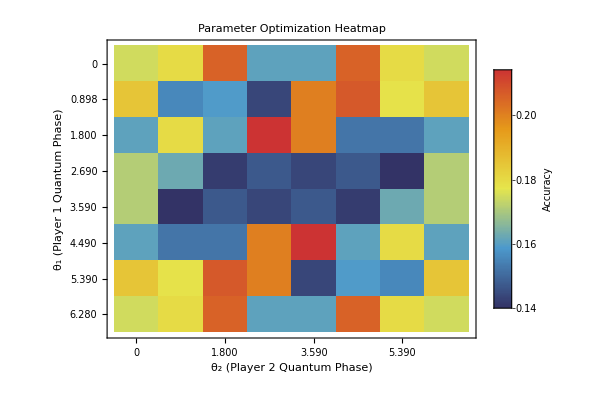

```mathematica
visualizeGridSearchResults[gridResults]
```

```mathematica
l1=1;
l2=1;
theta1 =N[gridResults["bestTheta1"]];
theta2=N[gridResults["bestTheta2"]];
```

```mathematica
results=processQuantumDataset[data,theta1,theta2,l1,l2];
```

Processing 579 rows with quantum model...

Parameters: θ1=2.69279, θ2=1.7952, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

```mathematica
getFirstNEntries[results,3]
```

Returning first 3 entries out of 579 total entries with extracted components.

{<|SQ→0.2588,ACQ1→0.0831,ACQ2→0.0406,NEGO→0.0188,CAP1→0.1083,CAP2→0.0633,WAR1→0.2335,WAR2→0.1935,prediction→SQ,groundtruth→SQ,Agent1→ESTONIA,Agent2→UNITED KINGDOM|>,<|SQ→0.0416,ACQ1→0.0066,ACQ2→0.395,NEGO→0.044,CAP1→0.0342,CAP2→0.1183,WAR1→0.1283,WAR2→0.232,prediction→ACQ2,groundtruth→SQ,Agent1→FRANCE,Agent2→CHILE|>,<|SQ→0.4087,ACQ1→0.0728,ACQ2→0.0789,NEGO→0.1262,CAP1→0.0068,CAP2→0.0279,WAR1→0.2706,WAR2→0.0081,prediction→SQ,groundtruth→SQ,Agent1→ARGENTINA,Agent2→FRANCE|>}

```mathematica
accuracy=calculateQuantumAccuracy[results];
Print["Final Accuracy: ",N[accuracy]];
```

Final Accuracy: 0.214162

```mathematica
plotQuantumConfusionMatrix[results,theta1,theta2,l1,l2,"Quantum-Like Signorino Model Confusion Matrix"]
```

Quantum-Like Signorino Model Confusion Matrix

θ1 = 2.69279 θ2 = 1.7952 λ1 = 1 λ2 = 1 | Accuracy = 0.214162

Actual \ Predicted | ACQ1 | ACQ2 | CAP1 | CAP2 | NEGO | SQ | WAR1
ACQ1 | 0 | 2 | 2 | 0 | 0 | 0 | 2
ACQ2 | 0 | 52 | 2 | 0 | 0 | 24 | 21
CAP1 | 0 | 18 | 6 | 0 | 0 | 12 | 20
CAP2 | 0 | 45 | 3 | 0 | 0 | 27 | 24
NEGO | 0 | 26 | 7 | 0 | 0 | 39 | 27
SQ | 0 | 27 | 4 | 0 | 0 | 41 | 27
WAR1 | 0 | 38 | 4 | 0 | 0 | 32 | 25

#### Setting 2: Lambda1 = 0.5 | Lambda2 = 0.5

```mathematica
datasetPath = "/Users/162191/Documents/GitHub/quantum_international_interaction_game/dataset/balanced_data.csv" 
(* "D:\\home\\Documents\\Github\\quantum_international_interaction_game\\dataset\\balanced_data.csv"; *)
data=loadData[datasetPath];
```

/Users/162191/Documents/GitHub/quantum_international_interaction_game/dataset/balanced_data.csv

Loading CSV file: /Users/162191/Documents/GitHub/quantum_international_interaction_game/dataset/balanced_data.csv

Loaded 579 rows with 149 columns

```mathematica
gridsize = 8;
l1 =0.5;
l2=0.5;
theta1Range=createThetaRange[0,2*Pi,gridsize];
theta2Range=createThetaRange[0,2*Pi,gridsize];
```

```mathematica
gridResults=gridSearchQuantumThetas[data,theta1Range,theta2Range,l1,l2];
Print["Best parameters: θ1=",gridResults["bestTheta1"],", θ2=",gridResults["bestTheta2"]];
Print["Best accuracy: ",gridResults["bestAccuracy"]];
```

Starting grid search over 64 parameter combinations...

Theta1 range: {0,(2 π)/7,(4 π)/7,(6 π)/7,(8 π)/7,(10 π)/7,(12 π)/7,2 π}

Theta2 range: {0,(2 π)/7,(4 π)/7,(6 π)/7,(8 π)/7,(10 π)/7,(12 π)/7,2 π}

Lambda1 = 0.5, Lambda2 = 0.5

Dataset size: 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=0, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

New best found: θ1=0, θ2=0, Accuracy=0.17962

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=(2 π)/7, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

New best found: θ1=0, θ2=(2 π)/7, Accuracy=0.183074

Progress: 3/64 (4.69%)

Elapsed: 0.81 min, Estimated remaining: 16. min

Current best: θ1=0, θ2=(2 π)/7, Accuracy=0.183074

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=(4 π)/7, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=(6 π)/7, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=(8 π)/7, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 6/64 (9.38%)

Elapsed: 2.2 min, Estimated remaining: 21. min

Current best: θ1=0, θ2=(2 π)/7, Accuracy=0.183074

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=(10 π)/7, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=(12 π)/7, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=2 π, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 9/64 (14.1%)

Elapsed: 3.5 min, Estimated remaining: 21. min

Current best: θ1=0, θ2=(2 π)/7, Accuracy=0.183074

Processing 579 rows with quantum model...

Parameters: θ1=(2 π)/7, θ2=0, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(2 π)/7, θ2=(2 π)/7, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(2 π)/7, θ2=(4 π)/7, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 12/64 (18.8%)

Elapsed: 4.9 min, Estimated remaining: 21. min

Current best: θ1=0, θ2=(2 π)/7, Accuracy=0.183074

Processing 579 rows with quantum model...

Parameters: θ1=(2 π)/7, θ2=(6 π)/7, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(2 π)/7, θ2=(8 π)/7, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(2 π)/7, θ2=(10 π)/7, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 15/64 (23.4%)

Elapsed: 6.5 min, Estimated remaining: 21. min

Current best: θ1=0, θ2=(2 π)/7, Accuracy=0.183074

Processing 579 rows with quantum model...

Parameters: θ1=(2 π)/7, θ2=(12 π)/7, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(2 π)/7, θ2=2 π, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(4 π)/7, θ2=0, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

New best found: θ1=(4 π)/7, θ2=0, Accuracy=0.200345

Progress: 18/64 (28.1%)

Elapsed: 7.9 min, Estimated remaining: 20. min

Current best: θ1=(4 π)/7, θ2=0, Accuracy=0.200345

Processing 579 rows with quantum model...

Parameters: θ1=(4 π)/7, θ2=(2 π)/7, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(4 π)/7, θ2=(4 π)/7, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(4 π)/7, θ2=(6 π)/7, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 21/64 (32.8%)

Elapsed: 9.4 min, Estimated remaining: 19. min

Current best: θ1=(4 π)/7, θ2=0, Accuracy=0.200345

Processing 579 rows with quantum model...

Parameters: θ1=(4 π)/7, θ2=(8 π)/7, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(4 π)/7, θ2=(10 π)/7, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(4 π)/7, θ2=(12 π)/7, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 24/64 (37.5%)

Elapsed: 11. min, Estimated remaining: 18. min

Current best: θ1=(4 π)/7, θ2=0, Accuracy=0.200345

Processing 579 rows with quantum model...

Parameters: θ1=(4 π)/7, θ2=2 π, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(6 π)/7, θ2=0, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(6 π)/7, θ2=(2 π)/7, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 27/64 (42.2%)

Elapsed: 12. min, Estimated remaining: 17. min

Current best: θ1=(4 π)/7, θ2=0, Accuracy=0.200345

Processing 579 rows with quantum model...

Parameters: θ1=(6 π)/7, θ2=(4 π)/7, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

New best found: θ1=(6 π)/7, θ2=(4 π)/7, Accuracy=0.207254

Processing 579 rows with quantum model...

Parameters: θ1=(6 π)/7, θ2=(6 π)/7, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(6 π)/7, θ2=(8 π)/7, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 30/64 (46.9%)

Elapsed: 14. min, Estimated remaining: 16. min

Current best: θ1=(6 π)/7, θ2=(4 π)/7, Accuracy=0.207254

Processing 579 rows with quantum model...

Parameters: θ1=(6 π)/7, θ2=(10 π)/7, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(6 π)/7, θ2=(12 π)/7, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

New best found: θ1=(6 π)/7, θ2=(12 π)/7, Accuracy=0.229706

Processing 579 rows with quantum model...

Parameters: θ1=(6 π)/7, θ2=2 π, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 33/64 (51.6%)

Elapsed: 15. min, Estimated remaining: 14. min

Current best: θ1=(6 π)/7, θ2=(12 π)/7, Accuracy=0.229706

Processing 579 rows with quantum model...

Parameters: θ1=(8 π)/7, θ2=0, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(8 π)/7, θ2=(2 π)/7, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(8 π)/7, θ2=(4 π)/7, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 36/64 (56.3%)

Elapsed: 17. min, Estimated remaining: 13. min

Current best: θ1=(6 π)/7, θ2=(12 π)/7, Accuracy=0.229706

Processing 579 rows with quantum model...

Parameters: θ1=(8 π)/7, θ2=(6 π)/7, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(8 π)/7, θ2=(8 π)/7, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(8 π)/7, θ2=(10 π)/7, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 39/64 (60.9%)

Elapsed: 18. min, Estimated remaining: 12. min

Current best: θ1=(6 π)/7, θ2=(12 π)/7, Accuracy=0.229706

Processing 579 rows with quantum model...

Parameters: θ1=(8 π)/7, θ2=(12 π)/7, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(8 π)/7, θ2=2 π, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(10 π)/7, θ2=0, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 42/64 (65.6%)

Elapsed: 20. min, Estimated remaining: 10. min

Current best: θ1=(6 π)/7, θ2=(12 π)/7, Accuracy=0.229706

Processing 579 rows with quantum model...

Parameters: θ1=(10 π)/7, θ2=(2 π)/7, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(10 π)/7, θ2=(4 π)/7, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(10 π)/7, θ2=(6 π)/7, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 45/64 (70.3%)

Elapsed: 21. min, Estimated remaining: 8.9 min

Current best: θ1=(6 π)/7, θ2=(12 π)/7, Accuracy=0.229706

Processing 579 rows with quantum model...

Parameters: θ1=(10 π)/7, θ2=(8 π)/7, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(10 π)/7, θ2=(10 π)/7, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(10 π)/7, θ2=(12 π)/7, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 48/64 (75.%)

Elapsed: 23. min, Estimated remaining: 7.6 min

Current best: θ1=(6 π)/7, θ2=(12 π)/7, Accuracy=0.229706

Processing 579 rows with quantum model...

Parameters: θ1=(10 π)/7, θ2=2 π, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(12 π)/7, θ2=0, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(12 π)/7, θ2=(2 π)/7, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 51/64 (79.7%)

Elapsed: 24. min, Estimated remaining: 6.2 min

Current best: θ1=(6 π)/7, θ2=(12 π)/7, Accuracy=0.229706

Processing 579 rows with quantum model...

Parameters: θ1=(12 π)/7, θ2=(4 π)/7, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(12 π)/7, θ2=(6 π)/7, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(12 π)/7, θ2=(8 π)/7, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 54/64 (84.4%)

Elapsed: 26. min, Estimated remaining: 4.8 min

Current best: θ1=(6 π)/7, θ2=(12 π)/7, Accuracy=0.229706

Processing 579 rows with quantum model...

Parameters: θ1=(12 π)/7, θ2=(10 π)/7, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(12 π)/7, θ2=(12 π)/7, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(12 π)/7, θ2=2 π, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 57/64 (89.1%)

Elapsed: 27. min, Estimated remaining: 3.4 min

Current best: θ1=(6 π)/7, θ2=(12 π)/7, Accuracy=0.229706

Processing 579 rows with quantum model...

Parameters: θ1=2 π, θ2=0, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=2 π, θ2=(2 π)/7, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=2 π, θ2=(4 π)/7, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 60/64 (93.8%)

Elapsed: 29. min, Estimated remaining: 1.9 min

Current best: θ1=(6 π)/7, θ2=(12 π)/7, Accuracy=0.229706

Processing 579 rows with quantum model...

Parameters: θ1=2 π, θ2=(6 π)/7, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=2 π, θ2=(8 π)/7, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=2 π, θ2=(10 π)/7, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 63/64 (98.4%)

Elapsed: 30. min, Estimated remaining: 0.48 min

Current best: θ1=(6 π)/7, θ2=(12 π)/7, Accuracy=0.229706

Processing 579 rows with quantum model...

Parameters: θ1=2 π, θ2=(12 π)/7, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=2 π, θ2=2 π, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Grid search completed!

Total time: 31. minutes

Best parameters found:

θ1 = (6 π)/7

θ2 = (12 π)/7

Accuracy = 0.229706

Best parameters: θ1=(6 π)/7, θ2=(12 π)/7

Best accuracy: 0.229706

```mathematica
analyzeCurrentResults[gridResults]
```

analyzeCurrentResults[<|bestTheta1→(6 π)/7,bestTheta2→(12 π)/7,bestAccuracy→0.229706,allResults→{<|theta1→0,theta2→0,accuracy→0.17962,l1→0.5,l2→0.5|>,<|theta1→0,theta2→(2 π)/7,accuracy→0.183074,l1→0.5,l2→0.5|>,<|theta1→0,theta2→(4 π)/7,accuracy→0.158895,l1→0.5,l2→0.5|>,<|theta1→0,theta2→(6 π)/7,accuracy→0.174439,l1→0.5,l2→0.5|>,<|theta1→0,theta2→(8 π)/7,accuracy→0.174439,l1→0.5,l2→0.5|>,<|theta1→0,theta2→(10 π)/7,accuracy→0.158895,l1→0.5,l2→0.5|>,<|theta1→0,theta2→(12 π)/7,accuracy→0.183074,l1→0.5,l2→0.5|>,<|theta1→0,theta2→2 π,accuracy→0.17962,l1→0.5,l2→0.5|>,<|theta1→(2 π)/7,theta2→0,accuracy→0.176166,l1→0.5,l2→0.5|>,<|theta1→(2 π)/7,theta2→(2 π)/7,accuracy→0.172712,l1→0.5,l2→0.5|>,<|theta1→(2 π)/7,theta2→(4 π)/7,accuracy→0.181347,l1→0.5,l2→0.5|>,<|theta1→(2 π)/7,theta2→(6 π)/7,accuracy→0.174439,l1→0.5,l2→0.5|>,<|theta1→(2 π)/7,theta2→(8 π)/7,accuracy→0.131261,l1→0.5,l2→0.5|>,<|theta1→(2 π)/7,theta2→(10 π)/7,accuracy→0.162349,l1→0.5,l2→0.5|>,<|theta1→(2 π)/7,theta2→(12 π)/7,accuracy→0.181347,l1→0.5,l2→0.5|>,<|theta1→(2 π)/7,theta2→2 π,accuracy→0.176166,l1→0.5,l2→0.5|>,<|theta1→(4 π)/7,theta2→0,accuracy→0.200345,l1→0.5,l2→0.5|>,<|theta1→(4 π)/7,theta2→(2 π)/7,accuracy→0.157168,l1→0.5,l2→0.5|>,<|theta1→(4 π)/7,theta2→(4 π)/7,accuracy→0.162349,l1→0.5,l2→0.5|>,<|theta1→(4 π)/7,theta2→(6 π)/7,accuracy→0.170984,l1→0.5,l2→0.5|>,<|theta1→(4 π)/7,theta2→(8 π)/7,accuracy→0.146805,l1→0.5,l2→0.5|>,<|theta1→(4 π)/7,theta2→(10 π)/7,accuracy→0.17962,l1→0.5,l2→0.5|>,<|theta1→(4 π)/7,theta2→(12 π)/7,accuracy→0.200345,l1→0.5,l2→0.5|>,<|theta1→(4 π)/7,theta2→2 π,accuracy→0.200345,l1→0.5,l2→0.5|>,<|theta1→(6 π)/7,theta2→0,accuracy→0.162349,l1→0.5,l2→0.5|>,<|theta1→(6 π)/7,theta2→(2 π)/7,accuracy→0.151986,l1→0.5,l2→0.5|>,<|theta1→(6 π)/7,theta2→(4 π)/7,accuracy→0.207254,l1→0.5,l2→0.5|>,<|theta1→(6 π)/7,theta2→(6 π)/7,accuracy→0.148532,l1→0.5,l2→0.5|>,<|theta1→(6 π)/7,theta2→(8 π)/7,accuracy→0.139896,l1→0.5,l2→0.5|>,<|theta1→(6 π)/7,theta2→(10 π)/7,accuracy→0.205527,l1→0.5,l2→0.5|>,<|theta1→(6 π)/7,theta2→(12 π)/7,accuracy→0.229706,l1→0.5,l2→0.5|>,<|theta1→(6 π)/7,theta2→2 π,accuracy→0.162349,l1→0.5,l2→0.5|>,<|theta1→(8 π)/7,theta2→0,accuracy→0.162349,l1→0.5,l2→0.5|>,<|theta1→(8 π)/7,theta2→(2 π)/7,accuracy→0.229706,l1→0.5,l2→0.5|>,<|theta1→(8 π)/7,theta2→(4 π)/7,accuracy→0.205527,l1→0.5,l2→0.5|>,<|theta1→(8 π)/7,theta2→(6 π)/7,accuracy→0.139896,l1→0.5,l2→0.5|>,<|theta1→(8 π)/7,theta2→(8 π)/7,accuracy→0.148532,l1→0.5,l2→0.5|>,<|theta1→(8 π)/7,theta2→(10 π)/7,accuracy→0.207254,l1→0.5,l2→0.5|>,<|theta1→(8 π)/7,theta2→(12 π)/7,accuracy→0.151986,l1→0.5,l2→0.5|>,<|theta1→(8 π)/7,theta2→2 π,accuracy→0.162349,l1→0.5,l2→0.5|>,<|theta1→(10 π)/7,theta2→0,accuracy→0.200345,l1→0.5,l2→0.5|>,<|theta1→(10 π)/7,theta2→(2 π)/7,accuracy→0.200345,l1→0.5,l2→0.5|>,<|theta1→(10 π)/7,theta2→(4 π)/7,accuracy→0.17962,l1→0.5,l2→0.5|>,<|theta1→(10 π)/7,theta2→(6 π)/7,accuracy→0.146805,l1→0.5,l2→0.5|>,<|theta1→(10 π)/7,theta2→(8 π)/7,accuracy→0.170984,l1→0.5,l2→0.5|>,<|theta1→(10 π)/7,theta2→(10 π)/7,accuracy→0.162349,l1→0.5,l2→0.5|>,<|theta1→(10 π)/7,theta2→(12 π)/7,accuracy→0.157168,l1→0.5,l2→0.5|>,<|theta1→(10 π)/7,theta2→2 π,accuracy→0.200345,l1→0.5,l2→0.5|>,<|theta1→(12 π)/7,theta2→0,accuracy→0.176166,l1→0.5,l2→0.5|>,<|theta1→(12 π)/7,theta2→(2 π)/7,accuracy→0.181347,l1→0.5,l2→0.5|>,<|theta1→(12 π)/7,theta2→(4 π)/7,accuracy→0.162349,l1→0.5,l2→0.5|>,<|theta1→(12 π)/7,theta2→(6 π)/7,accuracy→0.131261,l1→0.5,l2→0.5|>,<|theta1→(12 π)/7,theta2→(8 π)/7,accuracy→0.174439,l1→0.5,l2→0.5|>,<|theta1→(12 π)/7,theta2→(10 π)/7,accuracy→0.181347,l1→0.5,l2→0.5|>,<|theta1→(12 π)/7,theta2→(12 π)/7,accuracy→0.172712,l1→0.5,l2→0.5|>,<|theta1→(12 π)/7,theta2→2 π,accuracy→0.176166,l1→0.5,l2→0.5|>,<|theta1→2 π,theta2→0,accuracy→0.17962,l1→0.5,l2→0.5|>,<|theta1→2 π,theta2→(2 π)/7,accuracy→0.183074,l1→0.5,l2→0.5|>,<|theta1→2 π,theta2→(4 π)/7,accuracy→0.158895,l1→0.5,l2→0.5|>,<|theta1→2 π,theta2→(6 π)/7,accuracy→0.174439,l1→0.5,l2→0.5|>,<|theta1→2 π,theta2→(8 π)/7,accuracy→0.174439,l1→0.5,l2→0.5|>,<|theta1→2 π,theta2→(10 π)/7,accuracy→0.158895,l1→0.5,l2→0.5|>,<|theta1→2 π,theta2→(12 π)/7,accuracy→0.183074,l1→0.5,l2→0.5|>,<|theta1→2 π,theta2→2 π,accuracy→0.17962,l1→0.5,l2→0.5|>},totalCombinations→64,l1→0.5,l2→0.5|>]

Grid Search Results Visualization

Parameter Space: 8 × 8 = 64 combinations

Best Parameters: θ₁ = 2.6930, θ₂ = 5.3860 → Accuracy = 0.2297 (22.97%)

Accuracy Range: 0.131 - 0.230

Summary Statistics:

• Mean Accuracy: 0.174

• Standard Deviation: 0.021

• Improvement over Random: 8.68% points

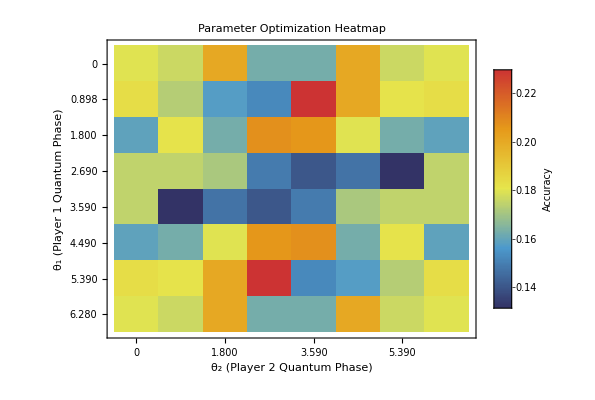

```mathematica
visualizeGridSearchResults[gridResults]
```

```mathematica
theta1 =N[gridResults["bestTheta1"]];
theta2=N[gridResults["bestTheta2"]];
```

```mathematica
results=processQuantumDataset[data,theta1,theta2,l1,l2];
```

Processing 579 rows with quantum model...

Parameters: θ1=2.69279, θ2=5.38559, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

```mathematica
getFirstNEntries[results,3]
```

Returning first 3 entries out of 579 total entries with extracted components.

{<|SQ→0.2657,ACQ1→0.066,ACQ2→0.1649,NEGO→0.0247,CAP1→0.1121,CAP2→0.0742,WAR1→0.1426,WAR2→0.1498,prediction→SQ,groundtruth→SQ,Agent1→ESTONIA,Agent2→UNITED KINGDOM|>,<|SQ→0.0687,ACQ1→0.0445,ACQ2→0.1936,NEGO→0.022,CAP1→0.1047,CAP2→0.144,WAR1→0.1499,WAR2→0.2726,prediction→WAR2,groundtruth→SQ,Agent1→FRANCE,Agent2→CHILE|>,<|SQ→0.4018,ACQ1→0.0844,ACQ2→0.1221,NEGO→0.0388,CAP1→0.0825,CAP2→0.0439,WAR1→0.1369,WAR2→0.0897,prediction→SQ,groundtruth→SQ,Agent1→ARGENTINA,Agent2→FRANCE|>}

```mathematica
accuracy=calculateQuantumAccuracy[results];
Print["Final Accuracy: ",N[accuracy]];
```

Final Accuracy: 0.229706

```mathematica
plotQuantumConfusionMatrix[results,theta1,theta2,l1,l2,"Quantum-Like Signorino Model Confusion Matrix"]
```

Quantum-Like Signorino Model Confusion Matrix

θ1 = 2.69279 θ2 = 5.38559 λ1 = 0.5 λ2 = 0.5 | Accuracy = 0.229706

Actual \ Predicted | ACQ1 | ACQ2 | CAP1 | CAP2 | NEGO | SQ | WAR1
ACQ1 | 0 | 3 | 2 | 0 | 0 | 1 | 0
ACQ2 | 0 | 68 | 0 | 0 | 0 | 28 | 3
CAP1 | 0 | 32 | 6 | 0 | 0 | 16 | 2
CAP2 | 0 | 58 | 1 | 0 | 0 | 39 | 1
NEGO | 0 | 36 | 7 | 0 | 0 | 52 | 4
SQ | 0 | 41 | 3 | 0 | 0 | 53 | 2
WAR1 | 0 | 54 | 6 | 0 | 0 | 33 | 6

#### Setting 3: Lambda1 = 2 | Lambda2 = 2

```mathematica
datasetPath = "/Users/162191/Documents/GitHub/quantum_international_interaction_game/dataset/balanced_data.csv";
(*"D:\\home\\Documents\\Github\\quantum_international_interaction_game\\dataset\\balanced_data.csv";*)
data=loadData[datasetPath];
```

Loading CSV file: /Users/162191/Documents/GitHub/quantum_international_interaction_game/dataset/balanced_data.csv

Loaded 579 rows with 149 columns

```mathematica
gridsize = 8;
l1 =2;
l2=2;
theta1Range=createThetaRange[0,2*Pi,gridsize];
theta2Range=createThetaRange[0,2*Pi,gridsize];
```

```mathematica
gridResults=gridSearchQuantumThetas[data,theta1Range,theta2Range,l1,l2];
Print["Best parameters: θ1=",gridResults["bestTheta1"],", θ2=",gridResults["bestTheta2"]];
Print["Best accuracy: ",gridResults["bestAccuracy"]];
```

Starting grid search over 64 parameter combinations...

Theta1 range: {0,(2 π)/7,(4 π)/7,(6 π)/7,(8 π)/7,(10 π)/7,(12 π)/7,2 π}

Theta2 range: {0,(2 π)/7,(4 π)/7,(6 π)/7,(8 π)/7,(10 π)/7,(12 π)/7,2 π}

Lambda1 = 2, Lambda2 = 2

Dataset size: 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=0, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

New best found: θ1=0, θ2=0, Accuracy=0.176166

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=(2 π)/7, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 3/64 (4.69%)

Elapsed: 0.84 min, Estimated remaining: 17. min

Current best: θ1=0, θ2=0, Accuracy=0.176166

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=(4 π)/7, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=(6 π)/7, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=(8 π)/7, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 6/64 (9.38%)

Elapsed: 2.2 min, Estimated remaining: 21. min

Current best: θ1=0, θ2=0, Accuracy=0.176166

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=(10 π)/7, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=(12 π)/7, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=2 π, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 9/64 (14.1%)

Elapsed: 3.6 min, Estimated remaining: 22. min

Current best: θ1=0, θ2=0, Accuracy=0.176166

Processing 579 rows with quantum model...

Parameters: θ1=(2 π)/7, θ2=0, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(2 π)/7, θ2=(2 π)/7, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(2 π)/7, θ2=(4 π)/7, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 12/64 (18.8%)

Elapsed: 5. min, Estimated remaining: 22. min

Current best: θ1=0, θ2=0, Accuracy=0.176166

Processing 579 rows with quantum model...

Parameters: θ1=(2 π)/7, θ2=(6 π)/7, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(2 π)/7, θ2=(8 π)/7, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(2 π)/7, θ2=(10 π)/7, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 15/64 (23.4%)

Elapsed: 6.6 min, Estimated remaining: 22. min

Current best: θ1=0, θ2=0, Accuracy=0.176166

Processing 579 rows with quantum model...

Parameters: θ1=(2 π)/7, θ2=(12 π)/7, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

New best found: θ1=(2 π)/7, θ2=(12 π)/7, Accuracy=0.177893

Processing 579 rows with quantum model...

Parameters: θ1=(2 π)/7, θ2=2 π, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(4 π)/7, θ2=0, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

New best found: θ1=(4 π)/7, θ2=0, Accuracy=0.207254

Progress: 18/64 (28.1%)

Elapsed: 8.1 min, Estimated remaining: 21. min

Current best: θ1=(4 π)/7, θ2=0, Accuracy=0.207254

Processing 579 rows with quantum model...

Parameters: θ1=(4 π)/7, θ2=(2 π)/7, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(4 π)/7, θ2=(4 π)/7, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(4 π)/7, θ2=(6 π)/7, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 21/64 (32.8%)

Elapsed: 9.6 min, Estimated remaining: 20. min

Current best: θ1=(4 π)/7, θ2=0, Accuracy=0.207254

Processing 579 rows with quantum model...

Parameters: θ1=(4 π)/7, θ2=(8 π)/7, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(4 π)/7, θ2=(10 π)/7, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(4 π)/7, θ2=(12 π)/7, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 24/64 (37.5%)

Elapsed: 11. min, Estimated remaining: 19. min

Current best: θ1=(4 π)/7, θ2=0, Accuracy=0.207254

Processing 579 rows with quantum model...

Parameters: θ1=(4 π)/7, θ2=2 π, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(6 π)/7, θ2=0, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(6 π)/7, θ2=(2 π)/7, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 27/64 (42.2%)

Elapsed: 13. min, Estimated remaining: 17. min

Current best: θ1=(4 π)/7, θ2=0, Accuracy=0.207254

Processing 579 rows with quantum model...

Parameters: θ1=(6 π)/7, θ2=(4 π)/7, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(6 π)/7, θ2=(6 π)/7, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(6 π)/7, θ2=(8 π)/7, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 30/64 (46.9%)

Elapsed: 14. min, Estimated remaining: 16. min

Current best: θ1=(4 π)/7, θ2=0, Accuracy=0.207254

Processing 579 rows with quantum model...

Parameters: θ1=(6 π)/7, θ2=(10 π)/7, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(6 π)/7, θ2=(12 π)/7, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(6 π)/7, θ2=2 π, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 33/64 (51.6%)

Elapsed: 16. min, Estimated remaining: 15. min

Current best: θ1=(4 π)/7, θ2=0, Accuracy=0.207254

Processing 579 rows with quantum model...

Parameters: θ1=(8 π)/7, θ2=0, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(8 π)/7, θ2=(2 π)/7, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(8 π)/7, θ2=(4 π)/7, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 36/64 (56.3%)

Elapsed: 17. min, Estimated remaining: 13. min

Current best: θ1=(4 π)/7, θ2=0, Accuracy=0.207254

Processing 579 rows with quantum model...

Parameters: θ1=(8 π)/7, θ2=(6 π)/7, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(8 π)/7, θ2=(8 π)/7, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(8 π)/7, θ2=(10 π)/7, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 39/64 (60.9%)

Elapsed: 19. min, Estimated remaining: 12. min

Current best: θ1=(4 π)/7, θ2=0, Accuracy=0.207254

Processing 579 rows with quantum model...

Parameters: θ1=(8 π)/7, θ2=(12 π)/7, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(8 π)/7, θ2=2 π, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(10 π)/7, θ2=0, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 42/64 (65.6%)

Elapsed: 20. min, Estimated remaining: 10. min

Current best: θ1=(4 π)/7, θ2=0, Accuracy=0.207254

Processing 579 rows with quantum model...

Parameters: θ1=(10 π)/7, θ2=(2 π)/7, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(10 π)/7, θ2=(4 π)/7, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(10 π)/7, θ2=(6 π)/7, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 45/64 (70.3%)

Elapsed: 21. min, Estimated remaining: 9.1 min

Current best: θ1=(4 π)/7, θ2=0, Accuracy=0.207254

Processing 579 rows with quantum model...

Parameters: θ1=(10 π)/7, θ2=(8 π)/7, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(10 π)/7, θ2=(10 π)/7, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(10 π)/7, θ2=(12 π)/7, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 48/64 (75.%)

Elapsed: 23. min, Estimated remaining: 7.7 min

Current best: θ1=(4 π)/7, θ2=0, Accuracy=0.207254

Processing 579 rows with quantum model...

Parameters: θ1=(10 π)/7, θ2=2 π, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(12 π)/7, θ2=0, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(12 π)/7, θ2=(2 π)/7, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 51/64 (79.7%)

Elapsed: 24. min, Estimated remaining: 6.2 min

Current best: θ1=(4 π)/7, θ2=0, Accuracy=0.207254

Processing 579 rows with quantum model...

Parameters: θ1=(12 π)/7, θ2=(4 π)/7, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(12 π)/7, θ2=(6 π)/7, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(12 π)/7, θ2=(8 π)/7, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 54/64 (84.4%)

Elapsed: 26. min, Estimated remaining: 4.8 min

Current best: θ1=(4 π)/7, θ2=0, Accuracy=0.207254

Processing 579 rows with quantum model...

Parameters: θ1=(12 π)/7, θ2=(10 π)/7, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(12 π)/7, θ2=(12 π)/7, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(12 π)/7, θ2=2 π, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 57/64 (89.1%)

Elapsed: 28. min, Estimated remaining: 3.4 min

Current best: θ1=(4 π)/7, θ2=0, Accuracy=0.207254

Processing 579 rows with quantum model...

Parameters: θ1=2 π, θ2=0, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=2 π, θ2=(2 π)/7, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=2 π, θ2=(4 π)/7, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 60/64 (93.8%)

Elapsed: 29. min, Estimated remaining: 1.9 min

Current best: θ1=(4 π)/7, θ2=0, Accuracy=0.207254

Processing 579 rows with quantum model...

Parameters: θ1=2 π, θ2=(6 π)/7, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=2 π, θ2=(8 π)/7, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=2 π, θ2=(10 π)/7, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 63/64 (98.4%)

Elapsed: 30. min, Estimated remaining: 0.48 min

Current best: θ1=(4 π)/7, θ2=0, Accuracy=0.207254

Processing 579 rows with quantum model...

Parameters: θ1=2 π, θ2=(12 π)/7, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=2 π, θ2=2 π, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Grid search completed!

Total time: 31. minutes

Best parameters found:

θ1 = (4 π)/7

θ2 = 0

Accuracy = 0.207254

Best parameters: θ1=(4 π)/7, θ2=0

Best accuracy: 0.207254

```mathematica
analyzeCurrentResults[gridResults]
```

analyzeCurrentResults[<|bestTheta1→(4 π)/7,bestTheta2→0,bestAccuracy→0.207254,allResults→{<|theta1→0,theta2→0,accuracy→0.176166,l1→2,l2→2|>,<|theta1→0,theta2→(2 π)/7,accuracy→0.150259,l1→2,l2→2|>,<|theta1→0,theta2→(4 π)/7,accuracy→0.157168,l1→2,l2→2|>,<|theta1→0,theta2→(6 π)/7,accuracy→0.169257,l1→2,l2→2|>,<|theta1→0,theta2→(8 π)/7,accuracy→0.169257,l1→2,l2→2|>,<|theta1→0,theta2→(10 π)/7,accuracy→0.157168,l1→2,l2→2|>,<|theta1→0,theta2→(12 π)/7,accuracy→0.150259,l1→2,l2→2|>,<|theta1→0,theta2→2 π,accuracy→0.176166,l1→2,l2→2|>,<|theta1→(2 π)/7,theta2→0,accuracy→0.172712,l1→2,l2→2|>,<|theta1→(2 π)/7,theta2→(2 π)/7,accuracy→0.145078,l1→2,l2→2|>,<|theta1→(2 π)/7,theta2→(4 π)/7,accuracy→0.157168,l1→2,l2→2|>,<|theta1→(2 π)/7,theta2→(6 π)/7,accuracy→0.153713,l1→2,l2→2|>,<|theta1→(2 π)/7,theta2→(8 π)/7,accuracy→0.143351,l1→2,l2→2|>,<|theta1→(2 π)/7,theta2→(10 π)/7,accuracy→0.148532,l1→2,l2→2|>,<|theta1→(2 π)/7,theta2→(12 π)/7,accuracy→0.177893,l1→2,l2→2|>,<|theta1→(2 π)/7,theta2→2 π,accuracy→0.172712,l1→2,l2→2|>,<|theta1→(4 π)/7,theta2→0,accuracy→0.207254,l1→2,l2→2|>,<|theta1→(4 π)/7,theta2→(2 π)/7,accuracy→0.16753,l1→2,l2→2|>,<|theta1→(4 π)/7,theta2→(4 π)/7,accuracy→0.158895,l1→2,l2→2|>,<|theta1→(4 π)/7,theta2→(6 π)/7,accuracy→0.16753,l1→2,l2→2|>,<|theta1→(4 π)/7,theta2→(8 π)/7,accuracy→0.146805,l1→2,l2→2|>,<|theta1→(4 π)/7,theta2→(10 π)/7,accuracy→0.16753,l1→2,l2→2|>,<|theta1→(4 π)/7,theta2→(12 π)/7,accuracy→0.176166,l1→2,l2→2|>,<|theta1→(4 π)/7,theta2→2 π,accuracy→0.207254,l1→2,l2→2|>,<|theta1→(6 π)/7,theta2→0,accuracy→0.169257,l1→2,l2→2|>,<|theta1→(6 π)/7,theta2→(2 π)/7,accuracy→0.151986,l1→2,l2→2|>,<|theta1→(6 π)/7,theta2→(4 π)/7,accuracy→0.2038,l1→2,l2→2|>,<|theta1→(6 π)/7,theta2→(6 π)/7,accuracy→0.153713,l1→2,l2→2|>,<|theta1→(6 π)/7,theta2→(8 π)/7,accuracy→0.132988,l1→2,l2→2|>,<|theta1→(6 π)/7,theta2→(10 π)/7,accuracy→0.189983,l1→2,l2→2|>,<|theta1→(6 π)/7,theta2→(12 π)/7,accuracy→0.202073,l1→2,l2→2|>,<|theta1→(6 π)/7,theta2→2 π,accuracy→0.169257,l1→2,l2→2|>,<|theta1→(8 π)/7,theta2→0,accuracy→0.169257,l1→2,l2→2|>,<|theta1→(8 π)/7,theta2→(2 π)/7,accuracy→0.202073,l1→2,l2→2|>,<|theta1→(8 π)/7,theta2→(4 π)/7,accuracy→0.189983,l1→2,l2→2|>,<|theta1→(8 π)/7,theta2→(6 π)/7,accuracy→0.132988,l1→2,l2→2|>,<|theta1→(8 π)/7,theta2→(8 π)/7,accuracy→0.153713,l1→2,l2→2|>,<|theta1→(8 π)/7,theta2→(10 π)/7,accuracy→0.2038,l1→2,l2→2|>,<|theta1→(8 π)/7,theta2→(12 π)/7,accuracy→0.151986,l1→2,l2→2|>,<|theta1→(8 π)/7,theta2→2 π,accuracy→0.169257,l1→2,l2→2|>,<|theta1→(10 π)/7,theta2→0,accuracy→0.207254,l1→2,l2→2|>,<|theta1→(10 π)/7,theta2→(2 π)/7,accuracy→0.176166,l1→2,l2→2|>,<|theta1→(10 π)/7,theta2→(4 π)/7,accuracy→0.16753,l1→2,l2→2|>,<|theta1→(10 π)/7,theta2→(6 π)/7,accuracy→0.146805,l1→2,l2→2|>,<|theta1→(10 π)/7,theta2→(8 π)/7,accuracy→0.16753,l1→2,l2→2|>,<|theta1→(10 π)/7,theta2→(10 π)/7,accuracy→0.158895,l1→2,l2→2|>,<|theta1→(10 π)/7,theta2→(12 π)/7,accuracy→0.16753,l1→2,l2→2|>,<|theta1→(10 π)/7,theta2→2 π,accuracy→0.207254,l1→2,l2→2|>,<|theta1→(12 π)/7,theta2→0,accuracy→0.172712,l1→2,l2→2|>,<|theta1→(12 π)/7,theta2→(2 π)/7,accuracy→0.177893,l1→2,l2→2|>,<|theta1→(12 π)/7,theta2→(4 π)/7,accuracy→0.148532,l1→2,l2→2|>,<|theta1→(12 π)/7,theta2→(6 π)/7,accuracy→0.143351,l1→2,l2→2|>,<|theta1→(12 π)/7,theta2→(8 π)/7,accuracy→0.153713,l1→2,l2→2|>,<|theta1→(12 π)/7,theta2→(10 π)/7,accuracy→0.157168,l1→2,l2→2|>,<|theta1→(12 π)/7,theta2→(12 π)/7,accuracy→0.145078,l1→2,l2→2|>,<|theta1→(12 π)/7,theta2→2 π,accuracy→0.172712,l1→2,l2→2|>,<|theta1→2 π,theta2→0,accuracy→0.176166,l1→2,l2→2|>,<|theta1→2 π,theta2→(2 π)/7,accuracy→0.150259,l1→2,l2→2|>,<|theta1→2 π,theta2→(4 π)/7,accuracy→0.157168,l1→2,l2→2|>,<|theta1→2 π,theta2→(6 π)/7,accuracy→0.169257,l1→2,l2→2|>,<|theta1→2 π,theta2→(8 π)/7,accuracy→0.169257,l1→2,l2→2|>,<|theta1→2 π,theta2→(10 π)/7,accuracy→0.157168,l1→2,l2→2|>,<|theta1→2 π,theta2→(12 π)/7,accuracy→0.150259,l1→2,l2→2|>,<|theta1→2 π,theta2→2 π,accuracy→0.176166,l1→2,l2→2|>},totalCombinations→64,l1→2,l2→2|>]

Grid Search Results Visualization

Parameter Space: 8 × 8 = 64 combinations

Best Parameters: θ₁ = 1.7950, θ₂ = 0 → Accuracy = 0.2073 (20.73%)

Accuracy Range: 0.133 - 0.207

Summary Statistics:

• Mean Accuracy: 0.167

• Standard Deviation: 0.019

• Improvement over Random: 6.44% points

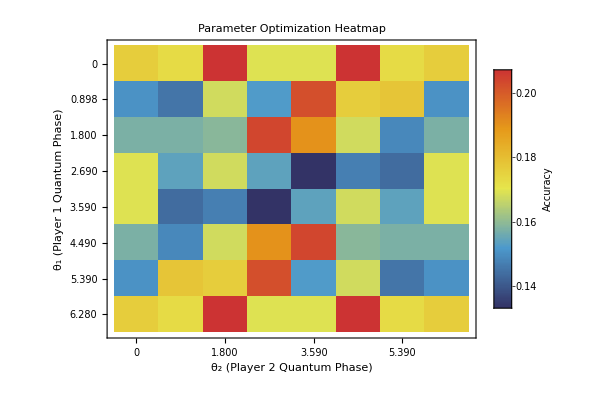

```mathematica
visualizeGridSearchResults[gridResults]
```

```mathematica
theta1 =N[gridResults["bestTheta1"]];
theta2=N[gridResults["bestTheta2"]];
```

```mathematica
results=processQuantumDataset[data,theta1,theta2,l1,l2];
```

Processing 579 rows with quantum model...

Parameters: θ1=1.7952, θ2=0., λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

```mathematica
getFirstNEntries[results,3]
```

Returning first 3 entries out of 579 total entries with extracted components.

{<|SQ→0.1857,ACQ1→0.0032,ACQ2→0.0306,NEGO→0.1633,CAP1→0.0974,CAP2→0.0143,WAR1→0.1946,WAR2→0.311,prediction→WAR2,groundtruth→SQ,Agent1→ESTONIA,Agent2→UNITED KINGDOM|>,<|SQ→0.0003,ACQ1→0.0645,ACQ2→0.0191,NEGO→0.042,CAP1→0.0026,CAP2→0.3465,WAR1→0.4075,WAR2→0.1175,prediction→WAR1,groundtruth→SQ,Agent1→FRANCE,Agent2→CHILE|>,<|SQ→0.2018,ACQ1→0.0001,ACQ2→0.1144,NEGO→0.1956,CAP1→0.0108,CAP2→0.0049,WAR1→0.4575,WAR2→0.0151,prediction→WAR1,groundtruth→SQ,Agent1→ARGENTINA,Agent2→FRANCE|>}

```mathematica
accuracy=calculateQuantumAccuracy[results];
Print["Final Accuracy: ",N[accuracy]];
```

Final Accuracy: 0.207254

```mathematica
plotQuantumConfusionMatrix[results,theta1,theta2,l1,l2,"Quantum-Like Signorino Model Confusion Matrix"]
```

Quantum-Like Signorino Model Confusion Matrix

θ1 = 1.7952 θ2 = 0. λ1 = 2 λ2 = 2 | Accuracy = 0.207254

Actual \ Predicted | ACQ1 | ACQ2 | CAP1 | CAP2 | NEGO | SQ | WAR1
ACQ1 | 0 | 0 | 3 | 0 | 0 | 1 | 2
ACQ2 | 2 | 10 | 1 | 0 | 6 | 14 | 66
CAP1 | 0 | 1 | 5 | 0 | 4 | 5 | 41
CAP2 | 1 | 5 | 1 | 0 | 5 | 17 | 70
NEGO | 3 | 5 | 11 | 0 | 10 | 16 | 54
SQ | 2 | 5 | 4 | 0 | 7 | 27 | 54
WAR1 | 1 | 3 | 4 | 0 | 8 | 15 | 68

#### Setting 4: Lambda1 = 0.1 | Lambda2 = 0.1

```mathematica
datasetPath = "/Users/162191/Documents/GitHub/quantum_international_interaction_game/dataset/balanced_data.csv" ;
(*"D:\\home\\Documents\\Github\\quantum_international_interaction_game\\dataset\\balanced_data.csv";*)
data=loadData[datasetPath];
```

Loading CSV file: /Users/162191/Documents/GitHub/quantum_international_interaction_game/dataset/balanced_data.csv

Loaded 579 rows with 149 columns

```mathematica
gridsize = 8;
l1 =0.1;
l2=0.1;
theta1Range=createThetaRange[0,2*Pi,gridsize];
theta2Range=createThetaRange[0,2*Pi,gridsize];
```

```mathematica
gridResults=gridSearchQuantumThetas[data,theta1Range,theta2Range,l1,l2];
Print["Best parameters: θ1=",gridResults["bestTheta1"],", θ2=",gridResults["bestTheta2"]];
Print["Best accuracy: ",gridResults["bestAccuracy"]];
```

Starting grid search over 64 parameter combinations...

Theta1 range: {0,(2 π)/7,(4 π)/7,(6 π)/7,(8 π)/7,(10 π)/7,(12 π)/7,2 π}

Theta2 range: {0,(2 π)/7,(4 π)/7,(6 π)/7,(8 π)/7,(10 π)/7,(12 π)/7,2 π}

Lambda1 = 0.1, Lambda2 = 0.1

Dataset size: 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=0, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

New best found: θ1=0, θ2=0, Accuracy=0.170984

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=(2 π)/7, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

New best found: θ1=0, θ2=(2 π)/7, Accuracy=0.172712

Progress: 3/64 (4.69%)

Elapsed: 0.83 min, Estimated remaining: 17. min

Current best: θ1=0, θ2=(2 π)/7, Accuracy=0.172712

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=(4 π)/7, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=(6 π)/7, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=(8 π)/7, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 6/64 (9.38%)

Elapsed: 2.2 min, Estimated remaining: 21. min

Current best: θ1=0, θ2=(2 π)/7, Accuracy=0.172712

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=(10 π)/7, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=(12 π)/7, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=2 π, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 9/64 (14.1%)

Elapsed: 3.5 min, Estimated remaining: 22. min

Current best: θ1=0, θ2=(2 π)/7, Accuracy=0.172712

Processing 579 rows with quantum model...

Parameters: θ1=(2 π)/7, θ2=0, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

New best found: θ1=(2 π)/7, θ2=0, Accuracy=0.177893

Processing 579 rows with quantum model...

Parameters: θ1=(2 π)/7, θ2=(2 π)/7, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(2 π)/7, θ2=(4 π)/7, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 12/64 (18.8%)

Elapsed: 4.9 min, Estimated remaining: 21. min

Current best: θ1=(2 π)/7, θ2=0, Accuracy=0.177893

Processing 579 rows with quantum model...

Parameters: θ1=(2 π)/7, θ2=(6 π)/7, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(2 π)/7, θ2=(8 π)/7, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(2 π)/7, θ2=(10 π)/7, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 15/64 (23.4%)

Elapsed: 6.4 min, Estimated remaining: 21. min

Current best: θ1=(2 π)/7, θ2=0, Accuracy=0.177893

Processing 579 rows with quantum model...

Parameters: θ1=(2 π)/7, θ2=(12 π)/7, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(2 π)/7, θ2=2 π, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(4 π)/7, θ2=0, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

New best found: θ1=(4 π)/7, θ2=0, Accuracy=0.212435

Progress: 18/64 (28.1%)

Elapsed: 7.8 min, Estimated remaining: 20. min

Current best: θ1=(4 π)/7, θ2=0, Accuracy=0.212435

Processing 579 rows with quantum model...

Parameters: θ1=(4 π)/7, θ2=(2 π)/7, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(4 π)/7, θ2=(4 π)/7, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(4 π)/7, θ2=(6 π)/7, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 21/64 (32.8%)

Elapsed: 9.2 min, Estimated remaining: 19. min

Current best: θ1=(4 π)/7, θ2=0, Accuracy=0.212435

Processing 579 rows with quantum model...

Parameters: θ1=(4 π)/7, θ2=(8 π)/7, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(4 π)/7, θ2=(10 π)/7, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(4 π)/7, θ2=(12 π)/7, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 24/64 (37.5%)

Elapsed: 11. min, Estimated remaining: 18. min

Current best: θ1=(4 π)/7, θ2=0, Accuracy=0.212435

Processing 579 rows with quantum model...

Parameters: θ1=(4 π)/7, θ2=2 π, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(6 π)/7, θ2=0, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(6 π)/7, θ2=(2 π)/7, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 27/64 (42.2%)

Elapsed: 12. min, Estimated remaining: 17. min

Current best: θ1=(4 π)/7, θ2=0, Accuracy=0.212435

Processing 579 rows with quantum model...

Parameters: θ1=(6 π)/7, θ2=(4 π)/7, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(6 π)/7, θ2=(6 π)/7, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(6 π)/7, θ2=(8 π)/7, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 30/64 (46.9%)

Elapsed: 14. min, Estimated remaining: 15. min

Current best: θ1=(4 π)/7, θ2=0, Accuracy=0.212435

Processing 579 rows with quantum model...

Parameters: θ1=(6 π)/7, θ2=(10 π)/7, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(6 π)/7, θ2=(12 π)/7, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

New best found: θ1=(6 π)/7, θ2=(12 π)/7, Accuracy=0.217617

Processing 579 rows with quantum model...

Parameters: θ1=(6 π)/7, θ2=2 π, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 33/64 (51.6%)

Elapsed: 15. min, Estimated remaining: 14. min

Current best: θ1=(6 π)/7, θ2=(12 π)/7, Accuracy=0.217617

Processing 579 rows with quantum model...

Parameters: θ1=(8 π)/7, θ2=0, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(8 π)/7, θ2=(2 π)/7, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(8 π)/7, θ2=(4 π)/7, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 36/64 (56.3%)

Elapsed: 17. min, Estimated remaining: 13. min

Current best: θ1=(6 π)/7, θ2=(12 π)/7, Accuracy=0.217617

Processing 579 rows with quantum model...

Parameters: θ1=(8 π)/7, θ2=(6 π)/7, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(8 π)/7, θ2=(8 π)/7, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(8 π)/7, θ2=(10 π)/7, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 39/64 (60.9%)

Elapsed: 18. min, Estimated remaining: 12. min

Current best: θ1=(6 π)/7, θ2=(12 π)/7, Accuracy=0.217617

Processing 579 rows with quantum model...

Parameters: θ1=(8 π)/7, θ2=(12 π)/7, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(8 π)/7, θ2=2 π, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(10 π)/7, θ2=0, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 42/64 (65.6%)

Elapsed: 20. min, Estimated remaining: 10. min

Current best: θ1=(6 π)/7, θ2=(12 π)/7, Accuracy=0.217617

Processing 579 rows with quantum model...

Parameters: θ1=(10 π)/7, θ2=(2 π)/7, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(10 π)/7, θ2=(4 π)/7, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(10 π)/7, θ2=(6 π)/7, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 45/64 (70.3%)

Elapsed: 21. min, Estimated remaining: 8.9 min

Current best: θ1=(6 π)/7, θ2=(12 π)/7, Accuracy=0.217617

Processing 579 rows with quantum model...

Parameters: θ1=(10 π)/7, θ2=(8 π)/7, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(10 π)/7, θ2=(10 π)/7, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(10 π)/7, θ2=(12 π)/7, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 48/64 (75.%)

Elapsed: 23. min, Estimated remaining: 7.5 min

Current best: θ1=(6 π)/7, θ2=(12 π)/7, Accuracy=0.217617

Processing 579 rows with quantum model...

Parameters: θ1=(10 π)/7, θ2=2 π, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(12 π)/7, θ2=0, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(12 π)/7, θ2=(2 π)/7, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 51/64 (79.7%)

Elapsed: 24. min, Estimated remaining: 6.1 min

Current best: θ1=(6 π)/7, θ2=(12 π)/7, Accuracy=0.217617

Processing 579 rows with quantum model...

Parameters: θ1=(12 π)/7, θ2=(4 π)/7, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(12 π)/7, θ2=(6 π)/7, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(12 π)/7, θ2=(8 π)/7, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 54/64 (84.4%)

Elapsed: 26. min, Estimated remaining: 4.7 min

Current best: θ1=(6 π)/7, θ2=(12 π)/7, Accuracy=0.217617

Processing 579 rows with quantum model...

Parameters: θ1=(12 π)/7, θ2=(10 π)/7, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(12 π)/7, θ2=(12 π)/7, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(12 π)/7, θ2=2 π, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 57/64 (89.1%)

Elapsed: 27. min, Estimated remaining: 3.3 min

Current best: θ1=(6 π)/7, θ2=(12 π)/7, Accuracy=0.217617

Processing 579 rows with quantum model...

Parameters: θ1=2 π, θ2=0, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=2 π, θ2=(2 π)/7, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=2 π, θ2=(4 π)/7, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 60/64 (93.8%)

Elapsed: 28. min, Estimated remaining: 1.9 min

Current best: θ1=(6 π)/7, θ2=(12 π)/7, Accuracy=0.217617

Processing 579 rows with quantum model...

Parameters: θ1=2 π, θ2=(6 π)/7, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=2 π, θ2=(8 π)/7, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=2 π, θ2=(10 π)/7, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 63/64 (98.4%)

Elapsed: 30. min, Estimated remaining: 0.47 min

Current best: θ1=(6 π)/7, θ2=(12 π)/7, Accuracy=0.217617

Processing 579 rows with quantum model...

Parameters: θ1=2 π, θ2=(12 π)/7, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=2 π, θ2=2 π, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Grid search completed!

Total time: 31. minutes

Best parameters found:

θ1 = (6 π)/7

θ2 = (12 π)/7

Accuracy = 0.217617

Best parameters: θ1=(6 π)/7, θ2=(12 π)/7

Best accuracy: 0.217617

```mathematica
analyzeCurrentResults[gridResults]
```

analyzeCurrentResults[<|bestTheta1→(6 π)/7,bestTheta2→(12 π)/7,bestAccuracy→0.217617,allResults→{<|theta1→0,theta2→0,accuracy→0.170984,l1→0.1,l2→0.1|>,<|theta1→0,theta2→(2 π)/7,accuracy→0.172712,l1→0.1,l2→0.1|>,<|theta1→0,theta2→(4 π)/7,accuracy→0.160622,l1→0.1,l2→0.1|>,<|theta1→0,theta2→(6 π)/7,accuracy→0.172712,l1→0.1,l2→0.1|>,<|theta1→0,theta2→(8 π)/7,accuracy→0.172712,l1→0.1,l2→0.1|>,<|theta1→0,theta2→(10 π)/7,accuracy→0.160622,l1→0.1,l2→0.1|>,<|theta1→0,theta2→(12 π)/7,accuracy→0.172712,l1→0.1,l2→0.1|>,<|theta1→0,theta2→2 π,accuracy→0.170984,l1→0.1,l2→0.1|>,<|theta1→(2 π)/7,theta2→0,accuracy→0.177893,l1→0.1,l2→0.1|>,<|theta1→(2 π)/7,theta2→(2 π)/7,accuracy→0.162349,l1→0.1,l2→0.1|>,<|theta1→(2 π)/7,theta2→(4 π)/7,accuracy→0.170984,l1→0.1,l2→0.1|>,<|theta1→(2 π)/7,theta2→(6 π)/7,accuracy→0.170984,l1→0.1,l2→0.1|>,<|theta1→(2 π)/7,theta2→(8 π)/7,accuracy→0.16753,l1→0.1,l2→0.1|>,<|theta1→(2 π)/7,theta2→(10 π)/7,accuracy→0.162349,l1→0.1,l2→0.1|>,<|theta1→(2 π)/7,theta2→(12 π)/7,accuracy→0.176166,l1→0.1,l2→0.1|>,<|theta1→(2 π)/7,theta2→2 π,accuracy→0.177893,l1→0.1,l2→0.1|>,<|theta1→(4 π)/7,theta2→0,accuracy→0.212435,l1→0.1,l2→0.1|>,<|theta1→(4 π)/7,theta2→(2 π)/7,accuracy→0.158895,l1→0.1,l2→0.1|>,<|theta1→(4 π)/7,theta2→(4 π)/7,accuracy→0.172712,l1→0.1,l2→0.1|>,<|theta1→(4 π)/7,theta2→(6 π)/7,accuracy→0.172712,l1→0.1,l2→0.1|>,<|theta1→(4 π)/7,theta2→(8 π)/7,accuracy→0.164076,l1→0.1,l2→0.1|>,<|theta1→(4 π)/7,theta2→(10 π)/7,accuracy→0.189983,l1→0.1,l2→0.1|>,<|theta1→(4 π)/7,theta2→(12 π)/7,accuracy→0.189983,l1→0.1,l2→0.1|>,<|theta1→(4 π)/7,theta2→2 π,accuracy→0.212435,l1→0.1,l2→0.1|>,<|theta1→(6 π)/7,theta2→0,accuracy→0.158895,l1→0.1,l2→0.1|>,<|theta1→(6 π)/7,theta2→(2 π)/7,accuracy→0.158895,l1→0.1,l2→0.1|>,<|theta1→(6 π)/7,theta2→(4 π)/7,accuracy→0.202073,l1→0.1,l2→0.1|>,<|theta1→(6 π)/7,theta2→(6 π)/7,accuracy→0.165803,l1→0.1,l2→0.1|>,<|theta1→(6 π)/7,theta2→(8 π)/7,accuracy→0.164076,l1→0.1,l2→0.1|>,<|theta1→(6 π)/7,theta2→(10 π)/7,accuracy→0.19171,l1→0.1,l2→0.1|>,<|theta1→(6 π)/7,theta2→(12 π)/7,accuracy→0.217617,l1→0.1,l2→0.1|>,<|theta1→(6 π)/7,theta2→2 π,accuracy→0.158895,l1→0.1,l2→0.1|>,<|theta1→(8 π)/7,theta2→0,accuracy→0.158895,l1→0.1,l2→0.1|>,<|theta1→(8 π)/7,theta2→(2 π)/7,accuracy→0.217617,l1→0.1,l2→0.1|>,<|theta1→(8 π)/7,theta2→(4 π)/7,accuracy→0.19171,l1→0.1,l2→0.1|>,<|theta1→(8 π)/7,theta2→(6 π)/7,accuracy→0.164076,l1→0.1,l2→0.1|>,<|theta1→(8 π)/7,theta2→(8 π)/7,accuracy→0.165803,l1→0.1,l2→0.1|>,<|theta1→(8 π)/7,theta2→(10 π)/7,accuracy→0.202073,l1→0.1,l2→0.1|>,<|theta1→(8 π)/7,theta2→(12 π)/7,accuracy→0.158895,l1→0.1,l2→0.1|>,<|theta1→(8 π)/7,theta2→2 π,accuracy→0.158895,l1→0.1,l2→0.1|>,<|theta1→(10 π)/7,theta2→0,accuracy→0.212435,l1→0.1,l2→0.1|>,<|theta1→(10 π)/7,theta2→(2 π)/7,accuracy→0.189983,l1→0.1,l2→0.1|>,<|theta1→(10 π)/7,theta2→(4 π)/7,accuracy→0.189983,l1→0.1,l2→0.1|>,<|theta1→(10 π)/7,theta2→(6 π)/7,accuracy→0.164076,l1→0.1,l2→0.1|>,<|theta1→(10 π)/7,theta2→(8 π)/7,accuracy→0.172712,l1→0.1,l2→0.1|>,<|theta1→(10 π)/7,theta2→(10 π)/7,accuracy→0.172712,l1→0.1,l2→0.1|>,<|theta1→(10 π)/7,theta2→(12 π)/7,accuracy→0.158895,l1→0.1,l2→0.1|>,<|theta1→(10 π)/7,theta2→2 π,accuracy→0.212435,l1→0.1,l2→0.1|>,<|theta1→(12 π)/7,theta2→0,accuracy→0.177893,l1→0.1,l2→0.1|>,<|theta1→(12 π)/7,theta2→(2 π)/7,accuracy→0.176166,l1→0.1,l2→0.1|>,<|theta1→(12 π)/7,theta2→(4 π)/7,accuracy→0.162349,l1→0.1,l2→0.1|>,<|theta1→(12 π)/7,theta2→(6 π)/7,accuracy→0.16753,l1→0.1,l2→0.1|>,<|theta1→(12 π)/7,theta2→(8 π)/7,accuracy→0.170984,l1→0.1,l2→0.1|>,<|theta1→(12 π)/7,theta2→(10 π)/7,accuracy→0.170984,l1→0.1,l2→0.1|>,<|theta1→(12 π)/7,theta2→(12 π)/7,accuracy→0.162349,l1→0.1,l2→0.1|>,<|theta1→(12 π)/7,theta2→2 π,accuracy→0.177893,l1→0.1,l2→0.1|>,<|theta1→2 π,theta2→0,accuracy→0.170984,l1→0.1,l2→0.1|>,<|theta1→2 π,theta2→(2 π)/7,accuracy→0.172712,l1→0.1,l2→0.1|>,<|theta1→2 π,theta2→(4 π)/7,accuracy→0.160622,l1→0.1,l2→0.1|>,<|theta1→2 π,theta2→(6 π)/7,accuracy→0.172712,l1→0.1,l2→0.1|>,<|theta1→2 π,theta2→(8 π)/7,accuracy→0.172712,l1→0.1,l2→0.1|>,<|theta1→2 π,theta2→(10 π)/7,accuracy→0.160622,l1→0.1,l2→0.1|>,<|theta1→2 π,theta2→(12 π)/7,accuracy→0.172712,l1→0.1,l2→0.1|>,<|theta1→2 π,theta2→2 π,accuracy→0.170984,l1→0.1,l2→0.1|>},totalCombinations→64,l1→0.1,l2→0.1|>]

Grid Search Results Visualization

Parameter Space: 8 × 8 = 64 combinations

Best Parameters: θ₁ = 2.6930, θ₂ = 5.3860 → Accuracy = 0.2176 (21.76%)

Accuracy Range: 0.159 - 0.218

Summary Statistics:

• Mean Accuracy: 0.175

• Standard Deviation: 0.016

• Improvement over Random: 7.48% points

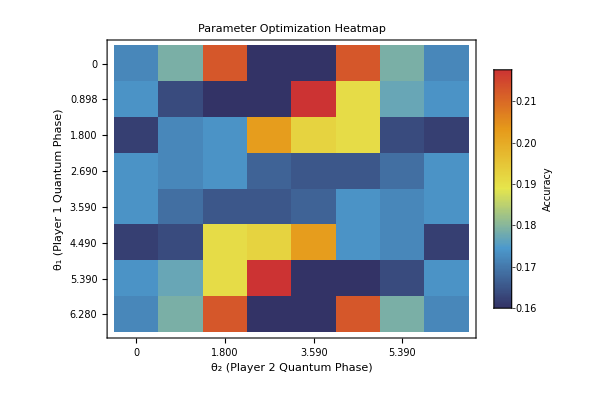

```mathematica
visualizeGridSearchResults[gridResults]
```

```mathematica
theta1 =N[gridResults["bestTheta1"]];
theta2=N[gridResults["bestTheta2"]];
```

```mathematica
results=processQuantumDataset[data,theta1,theta2,l1,l2];
```

Processing 579 rows with quantum model...

Parameters: θ1=2.69279, θ2=5.38559, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

```mathematica
getFirstNEntries[results,3]
```

Returning first 3 entries out of 579 total entries with extracted components.

{<|SQ→0.2507,ACQ1→0.1076,ACQ2→0.2332,NEGO→0.016,CAP1→0.1205,CAP2→0.0675,WAR1→0.0769,WAR2→0.1277,prediction→SQ,groundtruth→SQ,Agent1→ESTONIA,Agent2→UNITED KINGDOM|>,<|SQ→0.2111,ACQ1→0.1087,ACQ2→0.2418,NEGO→0.0137,CAP1→0.1245,CAP2→0.0744,WAR1→0.0751,WAR2→0.1507,prediction→ACQ2,groundtruth→SQ,Agent1→FRANCE,Agent2→CHILE|>,<|SQ→0.2656,ACQ1→0.1127,ACQ2→0.227,NEGO→0.0171,CAP1→0.1176,CAP2→0.0623,WAR1→0.0781,WAR2→0.1196,prediction→SQ,groundtruth→SQ,Agent1→ARGENTINA,Agent2→FRANCE|>}

```mathematica
accuracy=calculateQuantumAccuracy[results];
Print["Final Accuracy: ",N[accuracy]];
```

Final Accuracy: 0.217617

```mathematica
plotQuantumConfusionMatrix[results,theta1,theta2,l1,l2,"Quantum-Like Signorino Model Confusion Matrix"]
```

Quantum-Like Signorino Model Confusion Matrix

θ1 = 2.69279 θ2 = 5.38559 λ1 = 0.1 λ2 = 0.1 | Accuracy = 0.217617

Actual \ Predicted | ACQ1 | ACQ2 | CAP1 | CAP2 | NEGO | SQ | WAR1
ACQ1 | 0 | 4 | 0 | 0 | 0 | 2 | 0
ACQ2 | 0 | 66 | 0 | 0 | 0 | 33 | 0
CAP1 | 0 | 33 | 0 | 0 | 0 | 23 | 0
CAP2 | 0 | 54 | 0 | 0 | 0 | 45 | 0
NEGO | 0 | 35 | 0 | 0 | 0 | 64 | 0
SQ | 0 | 39 | 0 | 0 | 0 | 60 | 0
WAR1 | 0 | 56 | 0 | 0 | 0 | 43 | 0

#### Setting 5: Lambda1 = 10 | Lambda2 = 10

```mathematica
datasetPath ="/Users/162191/Documents/GitHub/quantum_international_interaction_game/dataset/balanced_data.csv" ;
(*"D:\\home\\Documents\\Github\\quantum_international_interaction_game\\dataset\\balanced_data.csv";*)
data=loadData[datasetPath];
```

Loading CSV file: /Users/162191/Documents/GitHub/quantum_international_interaction_game/dataset/balanced_data.csv

Loaded 579 rows with 149 columns

```mathematica
gridsize = 8;
l1 =10;
l2=10;
theta1Range=createThetaRange[0,2*Pi,gridsize];
theta2Range=createThetaRange[0,2*Pi,gridsize];
```

```mathematica
gridResults=gridSearchQuantumThetas[data,theta1Range,theta2Range,l1,l2];
Print["Best parameters: θ1=",gridResults["bestTheta1"],", θ2=",gridResults["bestTheta2"]];
Print["Best accuracy: ",gridResults["bestAccuracy"]];
```

Starting grid search over 64 parameter combinations...

Theta1 range: {0,(2 π)/7,(4 π)/7,(6 π)/7,(8 π)/7,(10 π)/7,(12 π)/7,2 π}

Theta2 range: {0,(2 π)/7,(4 π)/7,(6 π)/7,(8 π)/7,(10 π)/7,(12 π)/7,2 π}

Lambda1 = 10, Lambda2 = 10

Dataset size: 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=0, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

New best found: θ1=0, θ2=0, Accuracy=0.164076

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=(2 π)/7, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

New best found: θ1=0, θ2=(2 π)/7, Accuracy=0.200345

Progress: 3/64 (4.69%)

Elapsed: 0.82 min, Estimated remaining: 17. min

Current best: θ1=0, θ2=(2 π)/7, Accuracy=0.200345

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=(4 π)/7, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=(6 π)/7, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=(8 π)/7, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 6/64 (9.38%)

Elapsed: 2.2 min, Estimated remaining: 21. min

Current best: θ1=0, θ2=(2 π)/7, Accuracy=0.200345

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=(10 π)/7, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=(12 π)/7, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=2 π, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 9/64 (14.1%)

Elapsed: 3.5 min, Estimated remaining: 21. min

Current best: θ1=0, θ2=(2 π)/7, Accuracy=0.200345

Processing 579 rows with quantum model...

Parameters: θ1=(2 π)/7, θ2=0, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(2 π)/7, θ2=(2 π)/7, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(2 π)/7, θ2=(4 π)/7, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 12/64 (18.8%)

Elapsed: 4.9 min, Estimated remaining: 21. min

Current best: θ1=0, θ2=(2 π)/7, Accuracy=0.200345

Processing 579 rows with quantum model...

Parameters: θ1=(2 π)/7, θ2=(6 π)/7, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(2 π)/7, θ2=(8 π)/7, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(2 π)/7, θ2=(10 π)/7, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 15/64 (23.4%)

Elapsed: 6.4 min, Estimated remaining: 21. min

Current best: θ1=0, θ2=(2 π)/7, Accuracy=0.200345

Processing 579 rows with quantum model...

Parameters: θ1=(2 π)/7, θ2=(12 π)/7, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(2 π)/7, θ2=2 π, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(4 π)/7, θ2=0, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 18/64 (28.1%)

Elapsed: 7.8 min, Estimated remaining: 20. min

Current best: θ1=0, θ2=(2 π)/7, Accuracy=0.200345

Processing 579 rows with quantum model...

Parameters: θ1=(4 π)/7, θ2=(2 π)/7, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(4 π)/7, θ2=(4 π)/7, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(4 π)/7, θ2=(6 π)/7, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 21/64 (32.8%)

Elapsed: 9.2 min, Estimated remaining: 19. min

Current best: θ1=0, θ2=(2 π)/7, Accuracy=0.200345

Processing 579 rows with quantum model...

Parameters: θ1=(4 π)/7, θ2=(8 π)/7, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(4 π)/7, θ2=(10 π)/7, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(4 π)/7, θ2=(12 π)/7, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 24/64 (37.5%)

Elapsed: 11. min, Estimated remaining: 18. min

Current best: θ1=0, θ2=(2 π)/7, Accuracy=0.200345

Processing 579 rows with quantum model...

Parameters: θ1=(4 π)/7, θ2=2 π, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(6 π)/7, θ2=0, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(6 π)/7, θ2=(2 π)/7, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 27/64 (42.2%)

Elapsed: 12. min, Estimated remaining: 17. min

Current best: θ1=0, θ2=(2 π)/7, Accuracy=0.200345

Processing 579 rows with quantum model...

Parameters: θ1=(6 π)/7, θ2=(4 π)/7, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(6 π)/7, θ2=(6 π)/7, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(6 π)/7, θ2=(8 π)/7, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 30/64 (46.9%)

Elapsed: 14. min, Estimated remaining: 15. min

Current best: θ1=0, θ2=(2 π)/7, Accuracy=0.200345

Processing 579 rows with quantum model...

Parameters: θ1=(6 π)/7, θ2=(10 π)/7, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(6 π)/7, θ2=(12 π)/7, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(6 π)/7, θ2=2 π, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 33/64 (51.6%)

Elapsed: 15. min, Estimated remaining: 14. min

Current best: θ1=0, θ2=(2 π)/7, Accuracy=0.200345

Processing 579 rows with quantum model...

Parameters: θ1=(8 π)/7, θ2=0, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(8 π)/7, θ2=(2 π)/7, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(8 π)/7, θ2=(4 π)/7, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 36/64 (56.3%)

Elapsed: 17. min, Estimated remaining: 13. min

Current best: θ1=0, θ2=(2 π)/7, Accuracy=0.200345

Processing 579 rows with quantum model...

Parameters: θ1=(8 π)/7, θ2=(6 π)/7, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(8 π)/7, θ2=(8 π)/7, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(8 π)/7, θ2=(10 π)/7, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 39/64 (60.9%)

Elapsed: 18. min, Estimated remaining: 12. min

Current best: θ1=0, θ2=(2 π)/7, Accuracy=0.200345

Processing 579 rows with quantum model...

Parameters: θ1=(8 π)/7, θ2=(12 π)/7, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(8 π)/7, θ2=2 π, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(10 π)/7, θ2=0, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 42/64 (65.6%)

Elapsed: 20. min, Estimated remaining: 10. min

Current best: θ1=0, θ2=(2 π)/7, Accuracy=0.200345

Processing 579 rows with quantum model...

Parameters: θ1=(10 π)/7, θ2=(2 π)/7, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(10 π)/7, θ2=(4 π)/7, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(10 π)/7, θ2=(6 π)/7, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 45/64 (70.3%)

Elapsed: 21. min, Estimated remaining: 8.9 min

Current best: θ1=0, θ2=(2 π)/7, Accuracy=0.200345

Processing 579 rows with quantum model...

Parameters: θ1=(10 π)/7, θ2=(8 π)/7, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(10 π)/7, θ2=(10 π)/7, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(10 π)/7, θ2=(12 π)/7, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 48/64 (75.%)

Elapsed: 23. min, Estimated remaining: 7.6 min

Current best: θ1=0, θ2=(2 π)/7, Accuracy=0.200345

Processing 579 rows with quantum model...

Parameters: θ1=(10 π)/7, θ2=2 π, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(12 π)/7, θ2=0, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(12 π)/7, θ2=(2 π)/7, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 51/64 (79.7%)

Elapsed: 24. min, Estimated remaining: 6.1 min

Current best: θ1=0, θ2=(2 π)/7, Accuracy=0.200345

Processing 579 rows with quantum model...

Parameters: θ1=(12 π)/7, θ2=(4 π)/7, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(12 π)/7, θ2=(6 π)/7, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(12 π)/7, θ2=(8 π)/7, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 54/64 (84.4%)

Elapsed: 26. min, Estimated remaining: 4.7 min

Current best: θ1=0, θ2=(2 π)/7, Accuracy=0.200345

Processing 579 rows with quantum model...

Parameters: θ1=(12 π)/7, θ2=(10 π)/7, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(12 π)/7, θ2=(12 π)/7, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(12 π)/7, θ2=2 π, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 57/64 (89.1%)

Elapsed: 27. min, Estimated remaining: 3.3 min

Current best: θ1=0, θ2=(2 π)/7, Accuracy=0.200345

Processing 579 rows with quantum model...

Parameters: θ1=2 π, θ2=0, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=2 π, θ2=(2 π)/7, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=2 π, θ2=(4 π)/7, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 60/64 (93.8%)

Elapsed: 28. min, Estimated remaining: 1.9 min

Current best: θ1=0, θ2=(2 π)/7, Accuracy=0.200345

Processing 579 rows with quantum model...

Parameters: θ1=2 π, θ2=(6 π)/7, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=2 π, θ2=(8 π)/7, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=2 π, θ2=(10 π)/7, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 63/64 (98.4%)

Elapsed: 30. min, Estimated remaining: 0.47 min

Current best: θ1=0, θ2=(2 π)/7, Accuracy=0.200345

Processing 579 rows with quantum model...

Parameters: θ1=2 π, θ2=(12 π)/7, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=2 π, θ2=2 π, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Grid search completed!

Total time: 31. minutes

Best parameters found:

θ1 = 0

θ2 = (2 π)/7

Accuracy = 0.200345

Best parameters: θ1=0, θ2=(2 π)/7

Best accuracy: 0.200345

```mathematica
analyzeCurrentResults[gridResults]
```

analyzeCurrentResults[<|bestTheta1→0,bestTheta2→(2 π)/7,bestAccuracy→0.200345,allResults→{<|theta1→0,theta2→0,accuracy→0.164076,l1→10,l2→10|>,<|theta1→0,theta2→(2 π)/7,accuracy→0.200345,l1→10,l2→10|>,<|theta1→0,theta2→(4 π)/7,accuracy→0.162349,l1→10,l2→10|>,<|theta1→0,theta2→(6 π)/7,accuracy→0.16753,l1→10,l2→10|>,<|theta1→0,theta2→(8 π)/7,accuracy→0.16753,l1→10,l2→10|>,<|theta1→0,theta2→(10 π)/7,accuracy→0.162349,l1→10,l2→10|>,<|theta1→0,theta2→(12 π)/7,accuracy→0.200345,l1→10,l2→10|>,<|theta1→0,theta2→2 π,accuracy→0.164076,l1→10,l2→10|>,<|theta1→(2 π)/7,theta2→0,accuracy→0.177893,l1→10,l2→10|>,<|theta1→(2 π)/7,theta2→(2 π)/7,accuracy→0.181347,l1→10,l2→10|>,<|theta1→(2 π)/7,theta2→(4 π)/7,accuracy→0.164076,l1→10,l2→10|>,<|theta1→(2 π)/7,theta2→(6 π)/7,accuracy→0.17962,l1→10,l2→10|>,<|theta1→(2 π)/7,theta2→(8 π)/7,accuracy→0.138169,l1→10,l2→10|>,<|theta1→(2 π)/7,theta2→(10 π)/7,accuracy→0.146805,l1→10,l2→10|>,<|theta1→(2 π)/7,theta2→(12 π)/7,accuracy→0.186528,l1→10,l2→10|>,<|theta1→(2 π)/7,theta2→2 π,accuracy→0.177893,l1→10,l2→10|>,<|theta1→(4 π)/7,theta2→0,accuracy→0.196891,l1→10,l2→10|>,<|theta1→(4 π)/7,theta2→(2 π)/7,accuracy→0.151986,l1→10,l2→10|>,<|theta1→(4 π)/7,theta2→(4 π)/7,accuracy→0.172712,l1→10,l2→10|>,<|theta1→(4 π)/7,theta2→(6 π)/7,accuracy→0.157168,l1→10,l2→10|>,<|theta1→(4 π)/7,theta2→(8 π)/7,accuracy→0.131261,l1→10,l2→10|>,<|theta1→(4 π)/7,theta2→(10 π)/7,accuracy→0.141623,l1→10,l2→10|>,<|theta1→(4 π)/7,theta2→(12 π)/7,accuracy→0.188256,l1→10,l2→10|>,<|theta1→(4 π)/7,theta2→2 π,accuracy→0.196891,l1→10,l2→10|>,<|theta1→(6 π)/7,theta2→0,accuracy→0.160622,l1→10,l2→10|>,<|theta1→(6 π)/7,theta2→(2 π)/7,accuracy→0.158895,l1→10,l2→10|>,<|theta1→(6 π)/7,theta2→(4 π)/7,accuracy→0.164076,l1→10,l2→10|>,<|theta1→(6 π)/7,theta2→(6 π)/7,accuracy→0.143351,l1→10,l2→10|>,<|theta1→(6 π)/7,theta2→(8 π)/7,accuracy→0.139896,l1→10,l2→10|>,<|theta1→(6 π)/7,theta2→(10 π)/7,accuracy→0.172712,l1→10,l2→10|>,<|theta1→(6 π)/7,theta2→(12 π)/7,accuracy→0.196891,l1→10,l2→10|>,<|theta1→(6 π)/7,theta2→2 π,accuracy→0.160622,l1→10,l2→10|>,<|theta1→(8 π)/7,theta2→0,accuracy→0.160622,l1→10,l2→10|>,<|theta1→(8 π)/7,theta2→(2 π)/7,accuracy→0.196891,l1→10,l2→10|>,<|theta1→(8 π)/7,theta2→(4 π)/7,accuracy→0.172712,l1→10,l2→10|>,<|theta1→(8 π)/7,theta2→(6 π)/7,accuracy→0.139896,l1→10,l2→10|>,<|theta1→(8 π)/7,theta2→(8 π)/7,accuracy→0.143351,l1→10,l2→10|>,<|theta1→(8 π)/7,theta2→(10 π)/7,accuracy→0.164076,l1→10,l2→10|>,<|theta1→(8 π)/7,theta2→(12 π)/7,accuracy→0.158895,l1→10,l2→10|>,<|theta1→(8 π)/7,theta2→2 π,accuracy→0.160622,l1→10,l2→10|>,<|theta1→(10 π)/7,theta2→0,accuracy→0.196891,l1→10,l2→10|>,<|theta1→(10 π)/7,theta2→(2 π)/7,accuracy→0.188256,l1→10,l2→10|>,<|theta1→(10 π)/7,theta2→(4 π)/7,accuracy→0.141623,l1→10,l2→10|>,<|theta1→(10 π)/7,theta2→(6 π)/7,accuracy→0.131261,l1→10,l2→10|>,<|theta1→(10 π)/7,theta2→(8 π)/7,accuracy→0.157168,l1→10,l2→10|>,<|theta1→(10 π)/7,theta2→(10 π)/7,accuracy→0.172712,l1→10,l2→10|>,<|theta1→(10 π)/7,theta2→(12 π)/7,accuracy→0.151986,l1→10,l2→10|>,<|theta1→(10 π)/7,theta2→2 π,accuracy→0.196891,l1→10,l2→10|>,<|theta1→(12 π)/7,theta2→0,accuracy→0.177893,l1→10,l2→10|>,<|theta1→(12 π)/7,theta2→(2 π)/7,accuracy→0.186528,l1→10,l2→10|>,<|theta1→(12 π)/7,theta2→(4 π)/7,accuracy→0.146805,l1→10,l2→10|>,<|theta1→(12 π)/7,theta2→(6 π)/7,accuracy→0.138169,l1→10,l2→10|>,<|theta1→(12 π)/7,theta2→(8 π)/7,accuracy→0.17962,l1→10,l2→10|>,<|theta1→(12 π)/7,theta2→(10 π)/7,accuracy→0.164076,l1→10,l2→10|>,<|theta1→(12 π)/7,theta2→(12 π)/7,accuracy→0.181347,l1→10,l2→10|>,<|theta1→(12 π)/7,theta2→2 π,accuracy→0.177893,l1→10,l2→10|>,<|theta1→2 π,theta2→0,accuracy→0.164076,l1→10,l2→10|>,<|theta1→2 π,theta2→(2 π)/7,accuracy→0.200345,l1→10,l2→10|>,<|theta1→2 π,theta2→(4 π)/7,accuracy→0.162349,l1→10,l2→10|>,<|theta1→2 π,theta2→(6 π)/7,accuracy→0.16753,l1→10,l2→10|>,<|theta1→2 π,theta2→(8 π)/7,accuracy→0.16753,l1→10,l2→10|>,<|theta1→2 π,theta2→(10 π)/7,accuracy→0.162349,l1→10,l2→10|>,<|theta1→2 π,theta2→(12 π)/7,accuracy→0.200345,l1→10,l2→10|>,<|theta1→2 π,theta2→2 π,accuracy→0.164076,l1→10,l2→10|>},totalCombinations→64,l1→10,l2→10|>]

Grid Search Results Visualization

Parameter Space: 8 × 8 = 64 combinations

Best Parameters: θ₁ = 0, θ₂ = 0.8976 → Accuracy = 0.2003 (20.03%)

Accuracy Range: 0.131 - 0.200

Summary Statistics:

• Mean Accuracy: 0.168

• Standard Deviation: 0.019

• Improvement over Random: 5.75% points

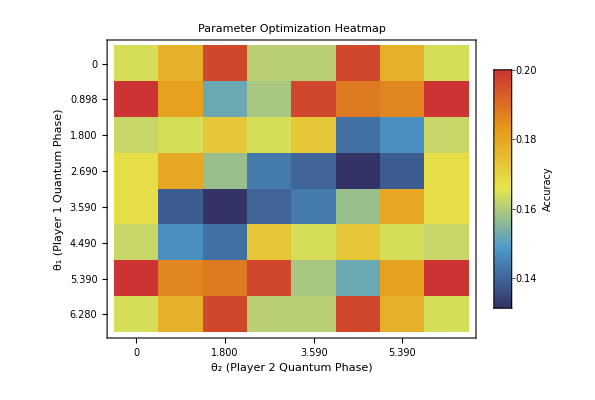

```mathematica
visualizeGridSearchResults[gridResults]
```

```mathematica
theta1 =N[gridResults["bestTheta1"]];
theta2=N[gridResults["bestTheta2"]];
```

```mathematica
results=processQuantumDataset[data,theta1,theta2,l1,l2];
```

Processing 579 rows with quantum model...

Parameters: θ1=0., θ2=0.897598, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

```mathematica
getFirstNEntries[results,3]
```

Returning first 3 entries out of 579 total entries with extracted components.

{<|SQ→0.4237,ACQ1→0.0014,ACQ2→0.,NEGO→0.3614,CAP1→0.0003,CAP2→0.,WAR1→0.1118,WAR2→0.1014,prediction→SQ,groundtruth→SQ,Agent1→ESTONIA,Agent2→UNITED KINGDOM|>,<|SQ→0.0013,ACQ1→0.,ACQ2→0.9969,NEGO→0.0007,CAP1→0.,CAP2→0.0003,WAR1→0.0008,WAR2→0.,prediction→ACQ2,groundtruth→SQ,Agent1→FRANCE,Agent2→CHILE|>,<|SQ→0.,ACQ1→0.,ACQ2→0.,NEGO→0.,CAP1→0.0001,CAP2→0.,WAR1→0.9994,WAR2→0.0005,prediction→WAR1,groundtruth→SQ,Agent1→ARGENTINA,Agent2→FRANCE|>}

```mathematica
accuracy=calculateQuantumAccuracy[results];
Print["Final Accuracy: ",N[accuracy]];
```

Final Accuracy: 0.200345

```mathematica
plotQuantumConfusionMatrix[results,theta1,theta2,l1,l2,"Quantum-Like Signorino Model Confusion Matrix"]
```

Quantum-Like Signorino Model Confusion Matrix

θ1 = 0. θ2 = 0.897598 λ1 = 10 λ2 = 10 | Accuracy = 0.200345

Actual \ Predicted | ACQ1 | ACQ2 | CAP1 | CAP2 | NEGO | SQ | WAR1
ACQ1 | 1 | 3 | 0 | 0 | 1 | 0 | 1
ACQ2 | 2 | 51 | 0 | 0 | 19 | 6 | 21
CAP1 | 3 | 20 | 0 | 0 | 12 | 8 | 13
CAP2 | 2 | 41 | 0 | 0 | 24 | 9 | 23
NEGO | 8 | 22 | 0 | 0 | 26 | 12 | 31
SQ | 5 | 26 | 0 | 0 | 20 | 10 | 38
WAR1 | 3 | 32 | 0 | 0 | 22 | 14 | 28

#### Setting 6: Lambda1 = 0.0001 | Lambda2 = 0.0001

```mathematica
datasetPath ="/Users/162191/Documents/GitHub/quantum_international_interaction_game/dataset/balanced_data.csv" ;
(*"D:\\home\\Documents\\Github\\quantum_international_interaction_game\\dataset\\balanced_data.csv";*)
data=loadData[datasetPath];
```

Loading CSV file: /Users/162191/Documents/GitHub/quantum_international_interaction_game/dataset/balanced_data.csv

Loaded 579 rows with 149 columns

```mathematica
gridsize = 8;
l1 =0.0001;
l2=0.0001;
theta1Range=createThetaRange[0,2*Pi,gridsize];
theta2Range=createThetaRange[0,2*Pi,gridsize];
```

```mathematica
gridResults=gridSearchQuantumThetas[data,theta1Range,theta2Range,l1,l2];
Print["Best parameters: θ1=",gridResults["bestTheta1"],", θ2=",gridResults["bestTheta2"]];
Print["Best accuracy: ",gridResults["bestAccuracy"]];
```

Starting grid search over 64 parameter combinations...

Theta1 range: {0,(2 π)/7,(4 π)/7,(6 π)/7,(8 π)/7,(10 π)/7,(12 π)/7,2 π}

Theta2 range: {0,(2 π)/7,(4 π)/7,(6 π)/7,(8 π)/7,(10 π)/7,(12 π)/7,2 π}

Lambda1 = 0.0001, Lambda2 = 0.0001

Dataset size: 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=0, λ1=0.0001, λ2=0.0001

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

New best found: θ1=0, θ2=0, Accuracy=0.170984

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=(2 π)/7, λ1=0.0001, λ2=0.0001

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

New best found: θ1=0, θ2=(2 π)/7, Accuracy=0.172712

Progress: 3/64 (4.69%)

Elapsed: 0.81 min, Estimated remaining: 16. min

Current best: θ1=0, θ2=(2 π)/7, Accuracy=0.172712

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=(4 π)/7, λ1=0.0001, λ2=0.0001

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=(6 π)/7, λ1=0.0001, λ2=0.0001

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=(8 π)/7, λ1=0.0001, λ2=0.0001

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 6/64 (9.38%)

Elapsed: 2.2 min, Estimated remaining: 21. min

Current best: θ1=0, θ2=(2 π)/7, Accuracy=0.172712

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=(10 π)/7, λ1=0.0001, λ2=0.0001

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=(12 π)/7, λ1=0.0001, λ2=0.0001

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=2 π, λ1=0.0001, λ2=0.0001

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 9/64 (14.1%)

Elapsed: 3.5 min, Estimated remaining: 21. min

Current best: θ1=0, θ2=(2 π)/7, Accuracy=0.172712

Processing 579 rows with quantum model...

Parameters: θ1=(2 π)/7, θ2=0, λ1=0.0001, λ2=0.0001

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(2 π)/7, θ2=(2 π)/7, λ1=0.0001, λ2=0.0001

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(2 π)/7, θ2=(4 π)/7, λ1=0.0001, λ2=0.0001

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 12/64 (18.8%)

Elapsed: 4.9 min, Estimated remaining: 21. min

Current best: θ1=0, θ2=(2 π)/7, Accuracy=0.172712

Processing 579 rows with quantum model...

Parameters: θ1=(2 π)/7, θ2=(6 π)/7, λ1=0.0001, λ2=0.0001

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(2 π)/7, θ2=(8 π)/7, λ1=0.0001, λ2=0.0001

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(2 π)/7, θ2=(10 π)/7, λ1=0.0001, λ2=0.0001

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 15/64 (23.4%)

Elapsed: 6.4 min, Estimated remaining: 21. min

Current best: θ1=0, θ2=(2 π)/7, Accuracy=0.172712

Processing 579 rows with quantum model...

Parameters: θ1=(2 π)/7, θ2=(12 π)/7, λ1=0.0001, λ2=0.0001

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

New best found: θ1=(2 π)/7, θ2=(12 π)/7, Accuracy=0.176166

Processing 579 rows with quantum model...

Parameters: θ1=(2 π)/7, θ2=2 π, λ1=0.0001, λ2=0.0001

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(4 π)/7, θ2=0, λ1=0.0001, λ2=0.0001

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

New best found: θ1=(4 π)/7, θ2=0, Accuracy=0.207254

Progress: 18/64 (28.1%)

Elapsed: 7.7 min, Estimated remaining: 20. min

Current best: θ1=(4 π)/7, θ2=0, Accuracy=0.207254

Processing 579 rows with quantum model...

Parameters: θ1=(4 π)/7, θ2=(2 π)/7, λ1=0.0001, λ2=0.0001

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(4 π)/7, θ2=(4 π)/7, λ1=0.0001, λ2=0.0001

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(4 π)/7, θ2=(6 π)/7, λ1=0.0001, λ2=0.0001

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 21/64 (32.8%)

Elapsed: 9.2 min, Estimated remaining: 19. min

Current best: θ1=(4 π)/7, θ2=0, Accuracy=0.207254

Processing 579 rows with quantum model...

Parameters: θ1=(4 π)/7, θ2=(8 π)/7, λ1=0.0001, λ2=0.0001

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(4 π)/7, θ2=(10 π)/7, λ1=0.0001, λ2=0.0001

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(4 π)/7, θ2=(12 π)/7, λ1=0.0001, λ2=0.0001

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 24/64 (37.5%)

Elapsed: 11. min, Estimated remaining: 18. min

Current best: θ1=(4 π)/7, θ2=0, Accuracy=0.207254

Processing 579 rows with quantum model...

Parameters: θ1=(4 π)/7, θ2=2 π, λ1=0.0001, λ2=0.0001

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(6 π)/7, θ2=0, λ1=0.0001, λ2=0.0001

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(6 π)/7, θ2=(2 π)/7, λ1=0.0001, λ2=0.0001

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 27/64 (42.2%)

Elapsed: 12. min, Estimated remaining: 17. min

Current best: θ1=(4 π)/7, θ2=0, Accuracy=0.207254

Processing 579 rows with quantum model...

Parameters: θ1=(6 π)/7, θ2=(4 π)/7, λ1=0.0001, λ2=0.0001

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(6 π)/7, θ2=(6 π)/7, λ1=0.0001, λ2=0.0001

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(6 π)/7, θ2=(8 π)/7, λ1=0.0001, λ2=0.0001

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 30/64 (46.9%)

Elapsed: 14. min, Estimated remaining: 15. min

Current best: θ1=(4 π)/7, θ2=0, Accuracy=0.207254

Processing 579 rows with quantum model...

Parameters: θ1=(6 π)/7, θ2=(10 π)/7, λ1=0.0001, λ2=0.0001

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(6 π)/7, θ2=(12 π)/7, λ1=0.0001, λ2=0.0001

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

New best found: θ1=(6 π)/7, θ2=(12 π)/7, Accuracy=0.214162

Processing 579 rows with quantum model...

Parameters: θ1=(6 π)/7, θ2=2 π, λ1=0.0001, λ2=0.0001

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 33/64 (51.6%)

Elapsed: 15. min, Estimated remaining: 14. min

Current best: θ1=(6 π)/7, θ2=(12 π)/7, Accuracy=0.214162

Processing 579 rows with quantum model...

Parameters: θ1=(8 π)/7, θ2=0, λ1=0.0001, λ2=0.0001

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(8 π)/7, θ2=(2 π)/7, λ1=0.0001, λ2=0.0001

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(8 π)/7, θ2=(4 π)/7, λ1=0.0001, λ2=0.0001

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 36/64 (56.3%)

Elapsed: 16. min, Estimated remaining: 13. min

Current best: θ1=(6 π)/7, θ2=(12 π)/7, Accuracy=0.214162

Processing 579 rows with quantum model...

Parameters: θ1=(8 π)/7, θ2=(6 π)/7, λ1=0.0001, λ2=0.0001

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(8 π)/7, θ2=(8 π)/7, λ1=0.0001, λ2=0.0001

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(8 π)/7, θ2=(10 π)/7, λ1=0.0001, λ2=0.0001

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 39/64 (60.9%)

Elapsed: 18. min, Estimated remaining: 12. min

Current best: θ1=(6 π)/7, θ2=(12 π)/7, Accuracy=0.214162

Processing 579 rows with quantum model...

Parameters: θ1=(8 π)/7, θ2=(12 π)/7, λ1=0.0001, λ2=0.0001

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(8 π)/7, θ2=2 π, λ1=0.0001, λ2=0.0001

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(10 π)/7, θ2=0, λ1=0.0001, λ2=0.0001

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 42/64 (65.6%)

Elapsed: 19. min, Estimated remaining: 10. min

Current best: θ1=(6 π)/7, θ2=(12 π)/7, Accuracy=0.214162

Processing 579 rows with quantum model...

Parameters: θ1=(10 π)/7, θ2=(2 π)/7, λ1=0.0001, λ2=0.0001

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(10 π)/7, θ2=(4 π)/7, λ1=0.0001, λ2=0.0001

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(10 π)/7, θ2=(6 π)/7, λ1=0.0001, λ2=0.0001

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 45/64 (70.3%)

Elapsed: 21. min, Estimated remaining: 8.8 min

Current best: θ1=(6 π)/7, θ2=(12 π)/7, Accuracy=0.214162

Processing 579 rows with quantum model...

Parameters: θ1=(10 π)/7, θ2=(8 π)/7, λ1=0.0001, λ2=0.0001

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(10 π)/7, θ2=(10 π)/7, λ1=0.0001, λ2=0.0001

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(10 π)/7, θ2=(12 π)/7, λ1=0.0001, λ2=0.0001

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 48/64 (75.%)

Elapsed: 22. min, Estimated remaining: 7.5 min

Current best: θ1=(6 π)/7, θ2=(12 π)/7, Accuracy=0.214162

Processing 579 rows with quantum model...

Parameters: θ1=(10 π)/7, θ2=2 π, λ1=0.0001, λ2=0.0001

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(12 π)/7, θ2=0, λ1=0.0001, λ2=0.0001

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(12 π)/7, θ2=(2 π)/7, λ1=0.0001, λ2=0.0001

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 51/64 (79.7%)

Elapsed: 24. min, Estimated remaining: 6.1 min

Current best: θ1=(6 π)/7, θ2=(12 π)/7, Accuracy=0.214162

Processing 579 rows with quantum model...

Parameters: θ1=(12 π)/7, θ2=(4 π)/7, λ1=0.0001, λ2=0.0001

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(12 π)/7, θ2=(6 π)/7, λ1=0.0001, λ2=0.0001

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(12 π)/7, θ2=(8 π)/7, λ1=0.0001, λ2=0.0001

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 54/64 (84.4%)

Elapsed: 25. min, Estimated remaining: 4.7 min

Current best: θ1=(6 π)/7, θ2=(12 π)/7, Accuracy=0.214162

Processing 579 rows with quantum model...

Parameters: θ1=(12 π)/7, θ2=(10 π)/7, λ1=0.0001, λ2=0.0001

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(12 π)/7, θ2=(12 π)/7, λ1=0.0001, λ2=0.0001

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=(12 π)/7, θ2=2 π, λ1=0.0001, λ2=0.0001

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 57/64 (89.1%)

Elapsed: 27. min, Estimated remaining: 3.3 min

Current best: θ1=(6 π)/7, θ2=(12 π)/7, Accuracy=0.214162

Processing 579 rows with quantum model...

Parameters: θ1=2 π, θ2=0, λ1=0.0001, λ2=0.0001

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=2 π, θ2=(2 π)/7, λ1=0.0001, λ2=0.0001

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=2 π, θ2=(4 π)/7, λ1=0.0001, λ2=0.0001

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 60/64 (93.8%)

Elapsed: 28. min, Estimated remaining: 1.9 min

Current best: θ1=(6 π)/7, θ2=(12 π)/7, Accuracy=0.214162

Processing 579 rows with quantum model...

Parameters: θ1=2 π, θ2=(6 π)/7, λ1=0.0001, λ2=0.0001

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=2 π, θ2=(8 π)/7, λ1=0.0001, λ2=0.0001

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=2 π, θ2=(10 π)/7, λ1=0.0001, λ2=0.0001

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Progress: 63/64 (98.4%)

Elapsed: 30. min, Estimated remaining: 0.47 min

Current best: θ1=(6 π)/7, θ2=(12 π)/7, Accuracy=0.214162

Processing 579 rows with quantum model...

Parameters: θ1=2 π, θ2=(12 π)/7, λ1=0.0001, λ2=0.0001

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=2 π, θ2=2 π, λ1=0.0001, λ2=0.0001

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

Grid search completed!

Total time: 31. minutes

Best parameters found:

θ1 = (6 π)/7

θ2 = (12 π)/7

Accuracy = 0.214162

Best parameters: θ1=(6 π)/7, θ2=(12 π)/7

Best accuracy: 0.214162

```mathematica
analyzeCurrentResults[gridResults]
```

analyzeCurrentResults[<|bestTheta1→(6 π)/7,bestTheta2→(12 π)/7,bestAccuracy→0.214162,allResults→{<|theta1→0,theta2→0,accuracy→0.170984,l1→0.0001,l2→0.0001|>,<|theta1→0,theta2→(2 π)/7,accuracy→0.172712,l1→0.0001,l2→0.0001|>,<|theta1→0,theta2→(4 π)/7,accuracy→0.160622,l1→0.0001,l2→0.0001|>,<|theta1→0,theta2→(6 π)/7,accuracy→0.172712,l1→0.0001,l2→0.0001|>,<|theta1→0,theta2→(8 π)/7,accuracy→0.172712,l1→0.0001,l2→0.0001|>,<|theta1→0,theta2→(10 π)/7,accuracy→0.160622,l1→0.0001,l2→0.0001|>,<|theta1→0,theta2→(12 π)/7,accuracy→0.172712,l1→0.0001,l2→0.0001|>,<|theta1→0,theta2→2 π,accuracy→0.170984,l1→0.0001,l2→0.0001|>,<|theta1→(2 π)/7,theta2→0,accuracy→0.170984,l1→0.0001,l2→0.0001|>,<|theta1→(2 π)/7,theta2→(2 π)/7,accuracy→0.150259,l1→0.0001,l2→0.0001|>,<|theta1→(2 π)/7,theta2→(4 π)/7,accuracy→0.170984,l1→0.0001,l2→0.0001|>,<|theta1→(2 π)/7,theta2→(6 π)/7,accuracy→0.169257,l1→0.0001,l2→0.0001|>,<|theta1→(2 π)/7,theta2→(8 π)/7,accuracy→0.164076,l1→0.0001,l2→0.0001|>,<|theta1→(2 π)/7,theta2→(10 π)/7,accuracy→0.16753,l1→0.0001,l2→0.0001|>,<|theta1→(2 π)/7,theta2→(12 π)/7,accuracy→0.176166,l1→0.0001,l2→0.0001|>,<|theta1→(2 π)/7,theta2→2 π,accuracy→0.170984,l1→0.0001,l2→0.0001|>,<|theta1→(4 π)/7,theta2→0,accuracy→0.207254,l1→0.0001,l2→0.0001|>,<|theta1→(4 π)/7,theta2→(2 π)/7,accuracy→0.157168,l1→0.0001,l2→0.0001|>,<|theta1→(4 π)/7,theta2→(4 π)/7,accuracy→0.172712,l1→0.0001,l2→0.0001|>,<|theta1→(4 π)/7,theta2→(6 π)/7,accuracy→0.172712,l1→0.0001,l2→0.0001|>,<|theta1→(4 π)/7,theta2→(8 π)/7,accuracy→0.164076,l1→0.0001,l2→0.0001|>,<|theta1→(4 π)/7,theta2→(10 π)/7,accuracy→0.184801,l1→0.0001,l2→0.0001|>,<|theta1→(4 π)/7,theta2→(12 π)/7,accuracy→0.186528,l1→0.0001,l2→0.0001|>,<|theta1→(4 π)/7,theta2→2 π,accuracy→0.207254,l1→0.0001,l2→0.0001|>,<|theta1→(6 π)/7,theta2→0,accuracy→0.160622,l1→0.0001,l2→0.0001|>,<|theta1→(6 π)/7,theta2→(2 π)/7,accuracy→0.165803,l1→0.0001,l2→0.0001|>,<|theta1→(6 π)/7,theta2→(4 π)/7,accuracy→0.195164,l1→0.0001,l2→0.0001|>,<|theta1→(6 π)/7,theta2→(6 π)/7,accuracy→0.165803,l1→0.0001,l2→0.0001|>,<|theta1→(6 π)/7,theta2→(8 π)/7,accuracy→0.164076,l1→0.0001,l2→0.0001|>,<|theta1→(6 π)/7,theta2→(10 π)/7,accuracy→0.19171,l1→0.0001,l2→0.0001|>,<|theta1→(6 π)/7,theta2→(12 π)/7,accuracy→0.214162,l1→0.0001,l2→0.0001|>,<|theta1→(6 π)/7,theta2→2 π,accuracy→0.160622,l1→0.0001,l2→0.0001|>,<|theta1→(8 π)/7,theta2→0,accuracy→0.160622,l1→0.0001,l2→0.0001|>,<|theta1→(8 π)/7,theta2→(2 π)/7,accuracy→0.214162,l1→0.0001,l2→0.0001|>,<|theta1→(8 π)/7,theta2→(4 π)/7,accuracy→0.19171,l1→0.0001,l2→0.0001|>,<|theta1→(8 π)/7,theta2→(6 π)/7,accuracy→0.164076,l1→0.0001,l2→0.0001|>,<|theta1→(8 π)/7,theta2→(8 π)/7,accuracy→0.165803,l1→0.0001,l2→0.0001|>,<|theta1→(8 π)/7,theta2→(10 π)/7,accuracy→0.195164,l1→0.0001,l2→0.0001|>,<|theta1→(8 π)/7,theta2→(12 π)/7,accuracy→0.165803,l1→0.0001,l2→0.0001|>,<|theta1→(8 π)/7,theta2→2 π,accuracy→0.160622,l1→0.0001,l2→0.0001|>,<|theta1→(10 π)/7,theta2→0,accuracy→0.207254,l1→0.0001,l2→0.0001|>,<|theta1→(10 π)/7,theta2→(2 π)/7,accuracy→0.186528,l1→0.0001,l2→0.0001|>,<|theta1→(10 π)/7,theta2→(4 π)/7,accuracy→0.184801,l1→0.0001,l2→0.0001|>,<|theta1→(10 π)/7,theta2→(6 π)/7,accuracy→0.164076,l1→0.0001,l2→0.0001|>,<|theta1→(10 π)/7,theta2→(8 π)/7,accuracy→0.172712,l1→0.0001,l2→0.0001|>,<|theta1→(10 π)/7,theta2→(10 π)/7,accuracy→0.172712,l1→0.0001,l2→0.0001|>,<|theta1→(10 π)/7,theta2→(12 π)/7,accuracy→0.157168,l1→0.0001,l2→0.0001|>,<|theta1→(10 π)/7,theta2→2 π,accuracy→0.207254,l1→0.0001,l2→0.0001|>,<|theta1→(12 π)/7,theta2→0,accuracy→0.170984,l1→0.0001,l2→0.0001|>,<|theta1→(12 π)/7,theta2→(2 π)/7,accuracy→0.176166,l1→0.0001,l2→0.0001|>,<|theta1→(12 π)/7,theta2→(4 π)/7,accuracy→0.16753,l1→0.0001,l2→0.0001|>,<|theta1→(12 π)/7,theta2→(6 π)/7,accuracy→0.164076,l1→0.0001,l2→0.0001|>,<|theta1→(12 π)/7,theta2→(8 π)/7,accuracy→0.169257,l1→0.0001,l2→0.0001|>,<|theta1→(12 π)/7,theta2→(10 π)/7,accuracy→0.170984,l1→0.0001,l2→0.0001|>,<|theta1→(12 π)/7,theta2→(12 π)/7,accuracy→0.150259,l1→0.0001,l2→0.0001|>,<|theta1→(12 π)/7,theta2→2 π,accuracy→0.170984,l1→0.0001,l2→0.0001|>,<|theta1→2 π,theta2→0,accuracy→0.170984,l1→0.0001,l2→0.0001|>,<|theta1→2 π,theta2→(2 π)/7,accuracy→0.172712,l1→0.0001,l2→0.0001|>,<|theta1→2 π,theta2→(4 π)/7,accuracy→0.160622,l1→0.0001,l2→0.0001|>,<|theta1→2 π,theta2→(6 π)/7,accuracy→0.172712,l1→0.0001,l2→0.0001|>,<|theta1→2 π,theta2→(8 π)/7,accuracy→0.172712,l1→0.0001,l2→0.0001|>,<|theta1→2 π,theta2→(10 π)/7,accuracy→0.160622,l1→0.0001,l2→0.0001|>,<|theta1→2 π,theta2→(12 π)/7,accuracy→0.172712,l1→0.0001,l2→0.0001|>,<|theta1→2 π,theta2→2 π,accuracy→0.170984,l1→0.0001,l2→0.0001|>},totalCombinations→64,l1→0.0001,l2→0.0001|>]

Grid Search Results Visualization

Parameter Space: 8 × 8 = 64 combinations

Best Parameters: θ₁ = 2.6930, θ₂ = 5.3860 → Accuracy = 0.2142 (21.42%)

Accuracy Range: 0.150 - 0.214

Summary Statistics:

• Mean Accuracy: 0.174

• Standard Deviation: 0.015

• Improvement over Random: 7.13% points

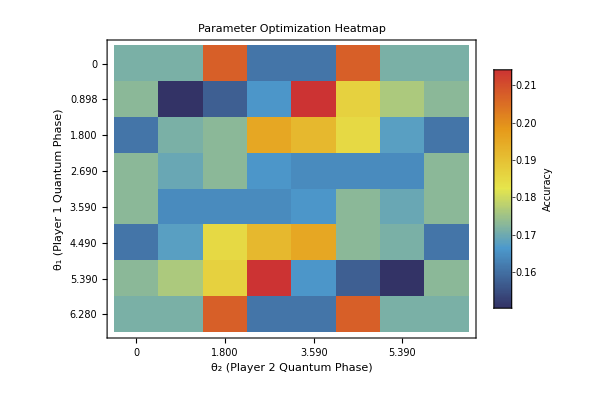

```mathematica
visualizeGridSearchResults[gridResults]
```

```mathematica
theta1 =N[gridResults["bestTheta1"]];
theta2=N[gridResults["bestTheta2"]];
```

```mathematica
results=processQuantumDataset[data,theta1,theta2,l1,l2];
```

Processing 579 rows with quantum model...

Parameters: θ1=2.69279, θ2=5.38559, λ1=0.0001, λ2=0.0001

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

```mathematica
getFirstNEntries[results,3]
```

Returning first 3 entries out of 579 total entries with extracted components.

{<|SQ→0.2457,ACQ1→0.1228,ACQ2→0.2457,NEGO→0.0139,CAP1→0.1228,CAP2→0.0631,WAR1→0.0631,WAR2→0.1228,prediction→ACQ2,groundtruth→SQ,Agent1→ESTONIA,Agent2→UNITED KINGDOM|>,<|SQ→0.2457,ACQ1→0.1228,ACQ2→0.2457,NEGO→0.0139,CAP1→0.1228,CAP2→0.0631,WAR1→0.0631,WAR2→0.1229,prediction→SQ,groundtruth→SQ,Agent1→FRANCE,Agent2→CHILE|>,<|SQ→0.2457,ACQ1→0.1228,ACQ2→0.2457,NEGO→0.0139,CAP1→0.1228,CAP2→0.0631,WAR1→0.0631,WAR2→0.1228,prediction→ACQ2,groundtruth→SQ,Agent1→ARGENTINA,Agent2→FRANCE|>}

```mathematica
accuracy=calculateQuantumAccuracy[results];
Print["Final Accuracy: ",N[accuracy]];
```

Final Accuracy: 0.214162

```mathematica
plotQuantumConfusionMatrix[results,theta1,theta2,l1,l2,"Quantum-Like Signorino Model Confusion Matrix"]
```

Quantum-Like Signorino Model Confusion Matrix

θ1 = 2.69279 θ2 = 5.38559 λ1 = 0.0001 λ2 = 0.0001 | Accuracy = 0.214162

Actual \ Predicted | ACQ1 | ACQ2 | CAP1 | CAP2 | NEGO | SQ | WAR1
ACQ1 | 0 | 4 | 0 | 0 | 0 | 2 | 0
ACQ2 | 0 | 63 | 0 | 0 | 0 | 36 | 0
CAP1 | 0 | 30 | 0 | 0 | 0 | 26 | 0
CAP2 | 0 | 54 | 0 | 0 | 0 | 45 | 0
NEGO | 0 | 33 | 0 | 0 | 0 | 66 | 0
SQ | 0 | 38 | 0 | 0 | 0 | 61 | 0
WAR1 | 0 | 55 | 0 | 0 | 0 | 44 | 0